# Retrospective evaluation of school-related measures on pre-vaccination transmission dynamics of SARS-CoV-2

## Benedetta Canfora, Rey Audie Escosio, Christiaan H. van Dorp, Otilia Boldea, Ana Nunes, and Ganna Rozhnova* Corresponding author: g.rozhnova@umcutrecht.nl

## Global parameters

```mathematica
(* Clear *)
$HistoryLength=0;
ClearSystemCache[]
ClearAll["Global`*"]
Clear["Subscript"]
Clear["Superscript"]
Clear["Subsuperscript"]
Off[General::munfl]
SetDirectory[NotebookDirectory[]];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
```

### Packages and parameters

```mathematica
(* External packages *)
AppendTo[$Path,"../packages"];
Needs["plotting`"];
Needs["preliminaries`"];

(*Remove["plotting`*"]
Get["../packages/plotting.m"]*)

(* Notebook parameters *)
ifShowFigs= True;
ifExportData = False;
ifExportFigs = False;
exportFormat={".pdf",".eps"};

(* Known constants *)
(* Age groups *)
numAgeGroups = 10;
listAgeGroups= Table[k, {k, 1, numAgeGroups}];
listChildren = Range[1,3];
listAdults = Range[4,10];
groupIndex = {listChildren, listAdults};

(* Samples *)
numAllSamples = 2000;
stepSamples=20; (* 20 corresponds to 100 samples *)
listSamples=Table[i,{i,1,numAllSamples,stepSamples}];
numSamples = Length[listSamples];

(* Variables *)
numVariables=5;
varNumbers= Table[j, {j, 1, numVariables}];
eqNumbers=Table[k,{k,1,numAgeGroups numVariables}];

(* Scenarios *)
scenarios={"Baseline", "Scenario1", "Scenario2"};
numScenarios = Length[scenarios];
```

### Important dates and time step

```mathematica
(* Date of starting simulations: February 25, 2020 *)
timeStart=0;
(* Date of start of the pandemic: February 26, 2020 *)

(* Date of last hospitalization/last data point: January 15, 2021 *)
timeEndData = Differences[{DateObject[{2020, 02, 26}],DateObject[{2021,01,15}]}]⟦1,1⟧+1+1 ; (* Jan 15 but starting with t=1 *)

(* Date of 2020 school vacation : June 10, 2020 *)
timeSchoolVacation=Differences[{DateObject[{2020, 02, 26}],DateObject[{2020, 06, 10}]}]⟦1,1⟧+1;

(* Integration end-time and time step *)
tStep=1;
tEnd=timeEndData;
tStart=timeStart;
times =Range[tStart,tEnd,tStep];
numTimes = Length[times];

(* Scenario time points *)
tStart1="February 25, 2020";
tEnd1="July 15, 2020";
tStart2="July 15, 2020";
tEnd2="January 16, 2021";
```

## Demography and contact matrices

### Seroprevalence data

```mathematica
totalMeanSero=2.9;
totalLowMeanSero=2.0;
totalHighMeanSero=4.2;
seroTotalDataAround = Around[totalMeanSero, {Abs[totalMeanSero - totalLowMeanSero], Abs[totalHighMeanSero-totalMeanSero]}];

seroprevalenceData=100 * Drop[Import["../data/PT_SEROPREVALENCE_DATA.csv"],1][[All,5;;7]];
seroAgeDataAround=Table[Around[seroprevalenceData[[i,1]],{seroprevalenceData[[i,1]] - seroprevalenceData[[i,2]],seroprevalenceData[[i,3]] - seroprevalenceData[[i,1]]}],{i,1,Length[seroprevalenceData]}];

seroDataMay28Around =Flatten[ {seroTotalDataAround, seroAgeDataAround}];
```

### Contact matrices from Vespignani et al.

```mathematica
(* Importing Data *)
(* https://github.com/mobs-lab/mixing-patterns *)
demographyData85=Import["../data/PT_DEMOGRAPHY_DATA_85.csv"]⟦All,2⟧;
contactDataBefore85=Import["../data/PT_CONTACT_MATRIX_TOTAL_85.csv"];
schoolContactDataBefore85=  11.41 * Import["../data/PT_CONTACT_MATRIX_SCHOOL_85.csv"];


(* Get the total contacts per participant *)
calculateTotalContsPerPar[conmat_, groupNo_] := Table[Total[conmat⟦k,All⟧],{k,groupNo}];
```

### Transforming the contact matrices from 86x86 to 10x10

```mathematica
(* Demographic data for 86+
https://www.pordata.pt/Portugal/Popula%C3%A7%C3%A3o+residente++m%C3%A9dia+anual+total+e+por+grupo+et%C3%A1rio-10 *)
demog86Plus = 316442;

(* Getting the ratio of lockdown contacts based on NL data *)
contactDataNLBefore10=Import["../data/NL_CONTACT_MATRIX_BEFORE_10.csv"];
contactDataNLAfter10=Import["../data/NL_CONTACT_MATRIX_AFTER_10.csv"];
contactRatioNL10=contactDataNLAfter10/contactDataNLBefore10;
demographyData10=Flatten[Import["../data/PT_DEMOGRAPHY_DATA_10.xlsx"]];

(* Function transforming the 1x86 age groups to 1x10 *)
transformList86to10[list85_]:=Total/@Join[Partition[list85,5]⟦1;;2⟧,Partition[list85,10]⟦2;;⟧,{list85⟦81;;⟧}];
demographyData86=Append[demographyData85, demog86Plus];
demographyData10Derived=transformList86to10[demographyData86];


(* Creating the 86x86 contact matrices *)
transformMatrix85to86[mat85_]:=Join[Join[mat85,{mat85⟦85⟧}],List/@(Join[mat85,{mat85⟦85⟧}]⟦All,85⟧ demographyData86⟦86⟧/demographyData86⟦85⟧), 2];
contactDataBefore86=transformMatrix85to86[contactDataBefore85];
schoolContactDataBefore86=transformMatrix85to86[schoolContactDataBefore85];


(* Creating the 10x10 contact matrices*)
transformMatrix86to10[mat86_] :=transformList86to10[Transpose[transformList86to10[Transpose[mat86]]] demographyData86]/demographyData10Derived;
contactDataBefore10=transformMatrix86to10[contactDataBefore86];
contactDataAfter10=contactDataBefore10 * contactRatioNL10 ;
schoolContactDataBefore10=transformMatrix86to10[schoolContactDataBefore86];


(* Assigning parameter variables *)
contactRates:=
Flatten[Table[{Subscript[b,{k,l}]->contactDataBefore10⟦k,l⟧,
Subscript[a,{k,l}]->contactDataAfter10⟦k,l⟧,
Subscript[s, {k, l}]->schoolContactDataBefore10[[k,l]]},
{k,1,numAgeGroups},{l,1,numAgeGroups}]];


(* Get the total contacts per participant *)
calculateContactsAgeGroupsBefore=calculateTotalContsPerPar[contactDataBefore10, numAgeGroups];
calculateSchoolContactsAgeGroupsBefore=calculateTotalContsPerPar[schoolContactDataBefore10, numAgeGroups];
calculateContactsAgeGroupsAfter=calculateTotalContsPerPar[contactDataAfter10, numAgeGroups];

(* Get the average contacts per participant *)
calculateAverageContactRateBefore=Sum[calculateContactsAgeGroupsBefore⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,listAgeGroups}];
calculateAverageContactRateSchoolsBefore=Sum[calculateSchoolContactsAgeGroupsBefore⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,listAgeGroups}];
calculateAverageContactRateAfter=Sum[calculateContactsAgeGroupsAfter⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,listAgeGroups}];
```

## Hospitalization data and estimated parameters

### Estimated parameters

```mathematica
(* Importing estimated parameters *)
estimatesData=Import["../data/PARAMETER_ESTIMATES.csv"];
headerParameters=estimatesData⟦1⟧;
estimatesData=Drop[estimatesData,1];
```

```mathematica
(* Assigning parameter variables *)
probabOfTransmEpsilon[sample_]:=ϵ->estimatesData⟦sample,1⟧;
probabOfTransmZeta[sample_]:=ζ-> estimatesData⟦sample,2⟧;
hospitalizationRate[sample_]:=Table[Subscript[ν,k]->estimatesData⟦sample,2+k⟧,{k,1,numAgeGroups}];
susceptibility[sample_]:=Flatten[Join[
Table[Subscript[β,k]->estimatesData⟦sample,14⟧ ,{k,1,3}],
Table[Subscript[β,k]->estimatesData⟦sample,15⟧ ,{k,4,7}],
Table[Subscript[β,k]->estimatesData⟦sample,16⟧ ,{k,8,10}]]];
latencyRate[sample_]:=α->estimatesData⟦sample,18⟧;
recoveryRate[sample_]:=γ->estimatesData⟦sample,19⟧;
rOverDisp[sample_]:=estimatesData⟦sample,17⟧;
logFuncParams[sample_]:={Subscript[xx, 0]-> estimatesData⟦sample,20⟧,Subscript[K, 0]-> estimatesData⟦sample,21⟧,
Subscript[xx, 1]-> estimatesData⟦sample,22⟧,Subscript[K, 1]-> estimatesData⟦sample,23⟧,
Subscript[xx, 2]-> estimatesData⟦sample,24⟧,Subscript[K, 2]-> estimatesData⟦sample,25⟧,
Subscript[xx, 3]-> estimatesData⟦sample,26⟧,Subscript[K, 3]-> estimatesData⟦sample,27⟧,
Subscript[xx, 4]-> estimatesData⟦sample,28⟧,Subscript[K, 4]-> estimatesData⟦sample,29⟧};
uParams[sample_]:={Subscript[u, 1]-> estimatesData⟦sample,30⟧,
Subscript[u, 2]-> estimatesData⟦sample,31⟧,
Subscript[u, 3]-> estimatesData⟦sample,32⟧,
Subscript[u, 4]-> estimatesData⟦sample,33⟧} ;
totalPop:=Table[Subscript[NN,k]-> demographyData10⟦k⟧,{k,listAgeGroups}];
initConds[sample_]:=Flatten[Table[{Subscript[S0,k]-> 1-estimatesData⟦sample,13⟧,
Subscript[EE0,k]-> 0.5 estimatesData⟦sample,13⟧,
Subscript[II0,k]-> 0.5 estimatesData⟦sample,13⟧,
Subscript[R0,k]-> 0,
Subscript[H0,k]-> 0},{k,listAgeGroups}]];


(* Table for all parameters *)
parameters[sample_]:=
Flatten[{contactRates,totalPop,probabOfTransmEpsilon[sample],probabOfTransmZeta[sample],hospitalizationRate[sample],initConds[sample],susceptibility[sample],logFuncParams[sample],uParams[sample],latencyRate[sample],recoveryRate[sample]}];
```

### Hospitalization data

```mathematica
(* Importing data *)hospitalizationData=Import["../data/PT_HOSPITALIZATION_DATA.csv"];
hospitalizationData=Drop[hospitalizationData,1];
hospitalizationDataTotal =Total[hospitalizationData, {2}];
hospitalizationDataGrouped = {Total[hospitalizationData[[All, 4;;10]], {2}], Total[hospitalizationData[[All, 1;;3]], {2}]};


(* Transition dates and their respective quantiles *)transitionDates=Table[DayPlus[{2020,02,25}, IntegerPart[Median[estimatesData⟦All,index⟧]]],{index,Range[20,28,2]}]; 
transitionDatesQuantiles025=Table[DayPlus[{2020,02,25}, IntegerPart[Quantile[estimatesData⟦All,index⟧,0.025]]],{index,Range[20,28,2]}]; 
transitionDatesQuantiles975=Table[DayPlus[{2020,02,25}, IntegerPart[Quantile[estimatesData⟦All,index⟧,0.975]]],{index,Range[20,28,2]}]; 
(* Range[20,28,2] are the indices for transition dates *)
```

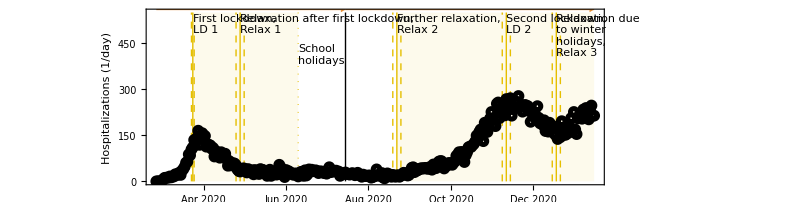

```mathematica
(* Plotting the diagram with the hospitalization data *)figDiag = plotDiagram[hospitalizationData, ticksVisible];
exportFigs[figDiag, "Fig1"];
```

## Scenarios

### School reduction factor, ζ_s

```mathematica
(* Calculation of the zeta_school parameter for Scenario 2 *)
schoolReductionEquation := 
Table[If[!(k==9 || k==10 ||l==9||l==10||(l==3 && k==1)||(l==1 && k==3)),Solve[(Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}])-reductionFactor Subscript[s,{k,l}]==(Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]),reductionFactor]⟦1⟧⟦1,2⟧],{k,1,numAgeGroups},{l,1,numAgeGroups}];
schoolReductionFactor[sample_]:=zetaSchools->Min[schoolReductionEquation /.Flatten[{contactRates,probabOfTransmZeta[sample],uParams[sample]}]][[1]];

(* Table for all parameters, including zeta_schools *)
parametersComplete[sample_]:=
Join[parameters[sample],{schoolReductionFactor[sample]}];
(* Sampled table for all parameters, from 2000 -> 100 *)parametersCompleteSampled = Table[parametersComplete[i],{i,1,numAllSamples,stepSamples}];

(* Saving the zeta_school parameters and obtaining the values *)
SRFFilePath = FileNameJoin[{"../results/solutions/"},StringJoin["SCHOOL_REDUCTION_FACTOR.wxf"]];
schRedFacObtained= Module[{SRF},
If[FileExistsQ[SRFFilePath],
SRF = Import[SRFFilePath,"WXF"],
SRF = Table[Min[schoolReductionEquation /.Flatten[{contactRates,probabOfTransmZeta[sample],uParams[sample]}]][[1]], {sample, 1, numAllSamples}];
Export[SRFFilePath,SRF,"WXF","CompressionLevel"->5];
SRF]];
```

### Expressions for contact matrices

```mathematica
contactMatrixBaseline[t_]:=
(Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]));


(* SCENARIO 1 *)
(* Not closing schools during the first lockdown and closing them for school holidays on tstartschoolvacation (10 June)*)
(* ζ can be introduced to reduce school contacts somewhat for the scenario with not closing schools after the first lockdown in 2020; the logic behind this is that there may be other measures implemented in schools such as masks, physical distancing, etc. *)
contactMatrixScenario1[t_]:=
((Subscript[b,{k,l}]-Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
Subscript[s,{k,l}] (1-1/(1+Exp[-10 (t-timeSchoolVacation)]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]));


(* Scenario 2 *)
(* Not opening schools after the summer holidays in 2020 *)
(* Zeta schools must be used to make sure that contacts are non-negative for the scenario with not opening schools after the summer holidays in 2020 *)
contactMatrixScenario2[t_]:=
(Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]-zetaSchools Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]-zetaSchools Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]-zetaSchools Subscript[s,{k,l}]));
```

## Equations and variables

### Model equations

```mathematica
(* Table of equations *)Table[{eq[Intervention_][1,k]:=Subscript[S,k]'[t]== - Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t],eq[Intervention_][2,k]:=Subscript[EE,k]'[t]== Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t]-α Subscript[EE,k][t],
eq[Intervention_][3,k]:=Subscript[II,k]'[t]== α Subscript[EE,k][t]-(γ +Subscript[ν,k]) Subscript[II,k][t],
eq[Intervention_][4,k]:=Subscript[R,k]'[t]==γ Subscript[II,k][t],
eq[Intervention_][5,k]:=Subscript[H,k]'[t]==Subscript[ν,k] Subscript[II,k][t]},{k,listAgeGroups}];
NNtot=Sum[Subscript[NN,k],{k,listAgeGroups}];

(* An if-condition for the contact matrix to use *)contactMatrixWhich[intervention_,t_]:=Which[intervention=="Baseline",contactMatrixBaseline[t],intervention=="Scenario1",contactMatrixScenario1[t],intervention=="Scenario2",contactMatrixScenario2[t], intervention=="Scenario2_Chris",
contactMatrixScenario2Chris[t],
True,$Failed ];

(* Force of infection *)Table[Subscript[λ,k][intervention][t]=ϵ Sum[contactMatrixWhich[intervention,t] Subscript[II,l][t]/Subscript[NN,l],{l,listAgeGroups}],{k,listAgeGroups},{intervention,scenarios} (*Iterate over interventions*)];

(* Final table of equations considering the interventions as the argument *)eqs[Intervention_]:=Table[eq[Intervention][j,k],{j,numVariables},{k,listAgeGroups}];
eqsList[Intervention_]:=Flatten[Flatten[eqs[Intervention]]];
```

### Variables

```mathematica
(* List of variables for each compartment and their totals *)varsS=Table[Subscript[S,k][t],{k,listAgeGroups}];
varsEE=Table[Subscript[EE,k][t],{k,listAgeGroups}];
varsII=Table[Subscript[II,k][t],{k,listAgeGroups}];
varsR=Table[Subscript[R,k][t],{k,listAgeGroups}];
varsH=Table[Subscript[H,k][t],{k,listAgeGroups}];

totS=Total[Total[varsS]];
totEE=Total[Total[varsEE]];
totII=Total[Total[varsII]];
totR=Total[Total[varsR]];
totH=Total[Total[varsH]];

totVars={totS,totEE,totII,totR,totH};


(* Indices of the compartments in all of the equations (will come in handy in NGM) *)
eqNumbersSusceptible = eqNumbers[[1 ;; numAgeGroups]];
eqNumbersExposed = eqNumbers[[numAgeGroups + 1 ;; 2 numAgeGroups]];
eqNumbersInfectious = eqNumbers[[2 numAgeGroups + 1 ;; 3 numAgeGroups]];


(* Flattened list of all variables*)
vars=Join[varsS,varsEE,varsII,varsR,varsH];
varsList=Flatten[vars];

(* Expression for the daily hospitalizations*)hospVars=Table[Subscript[ν,k] (Subscript[II,k][t]),{k,listAgeGroups}];
```

### Solving the model

```mathematica
(* Initial conditions *)
ICs=Table[ic[j,k],{j,varNumbers},{k,listAgeGroups}];
ICsList=Flatten[Flatten[ICs]];
(* Particularly for the compartments wherein we initially defined them as percentages from the total population (since N is constant through time)*)Table[ic[1,k]=Subscript[S0,k] Subscript[NN,k]==Subscript[S,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[2,k]=Subscript[EE0,k] Subscript[NN,k]==Subscript[EE,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[3,k]=Subscript[II0,k] Subscript[NN,k]==Subscript[II,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[4,k]=Subscript[R0,k] Subscript[NN,k]==Subscript[R,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[5,k]=Subscript[H0,k] Subscript[NN,k]==Subscript[H,k][t]/.{t->tStart},{k,listAgeGroups}];

(* Function solving the model *)solution[intervention_,pars_]:=NDSolve[Join[eqsList[intervention],ICsList]/.pars,
varsList,{t,tStart,tEnd}, Method->"StiffnessSwitching"];
(* and a for loop for each sample to solve it (this is still a function!) *)
solutionsForLoop[i_]:=Table[solution[scenarios[[i]],parametersCompleteSampled[[j]]],{j,1,Length[listSamples]}];
(* and finally importing/exporting them *)solutionsScenarios = importExportScenarioResults["SOLUTIONS", solutionsForLoop, "solutions"];
```

```mathematica
(* We aim to evaluate these solutions of the model with respect to certain trajectories (hospitalizations and susceptible population for seroprevalence) *)
trajectoriesVarForLoop[var_, i_, label_]:= 
Table[Table[Table[Evaluate[
(If[label === "SUSCEPTIBLE",
(If[k==1,(demographyData10⟦1⟧-86579)/demographyData10⟦1⟧,1] var⟦k⟧)+ If[k==1,86579,0],
var⟦k⟧]/.parametersCompleteSampled⟦j⟧)/.First@solutionsScenarios[[i]]⟦j⟧],
{t,tStart,tEnd,tStep}],
{j,1,Length[listSamples]}],
{k,listAgeGroups}]; 
importExport4Trajectories[var_, label_] := Module[{func},
func[i_] := trajectoriesVarForLoop[var, i,label];
importExportScenarioResults[label, func, "solutions"]];

(* and since we will regroup them according to age-specific or total populations, we need to sum them accordingly *)
summingGroups4Scenarios[variable_, index_] := Transpose[Table[Map[Total[#[[index[[i]], All, All]], {1}] &, variable], {i, 1, Length[index]}]];
```

i$::shdw: Symbol i$ appears in multiple contexts {plotting`,preliminaries`}; definitions in context plotting` may shadow or be shadowed by other definitions.

## Analysis

### Hospitalizations

```mathematica
(* Hospitalizations for the 10 age groups, for youth and adults, and for the total population *)hospitalizationScenarios=importExport4Trajectories[hospVars, "HOSPITALIZATION"];
hospitalizationScenariosGrouped = summingGroups4Scenarios[hospitalizationScenarios, groupIndex];
hospitalizationScenariosTotal = summingGroups4Scenarios[hospitalizationScenarios, {Range[1, 10]}];

(* Simulating a negative binomial distribution, we regenerate the hospitalizations *)
NBDReparameterized[m_,f_]:=NegativeBinomialDistribution[f,f/(f+m)];
hospSimulated[var_]:=Table[If[var⟦k⟧⟦sample⟧⟦t⟧>0,RandomVariate[NBDReparameterized[var⟦k⟧⟦sample⟧⟦t⟧,rOverDisp[listSamples⟦sample⟧]]],0],{k,listAgeGroups},{sample,1,Length[listSamples]},{t,1,Dimensions[var]⟦3⟧}];
hospitalizationSimulatedLoop[label_] := Module[{func},
func[i_] := hospSimulated[hospitalizationScenarios[[i]]];
     importExportScenarioResults[label, func, "solutions"]];

(* Getting simulated (noised) hospitalizations for the 10 age groups, for youth and adults, and for the total population *)hospitalizationSimulatedScenarios = hospitalizationSimulatedLoop["HOSPITALIZATION_SIMULATED"];
hospitalizationSimulatedScenariosGrouped = summingGroups4Scenarios[hospitalizationSimulatedScenarios, groupIndex];
hospitalizationSimulatedScenariosTotal = summingGroups4Scenarios[hospitalizationSimulatedScenarios, {Range[1, 10]}];
```

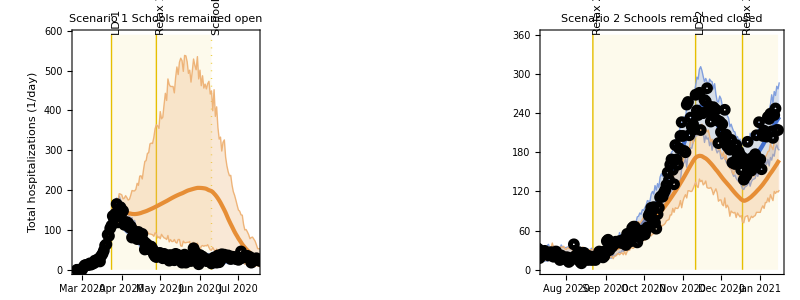
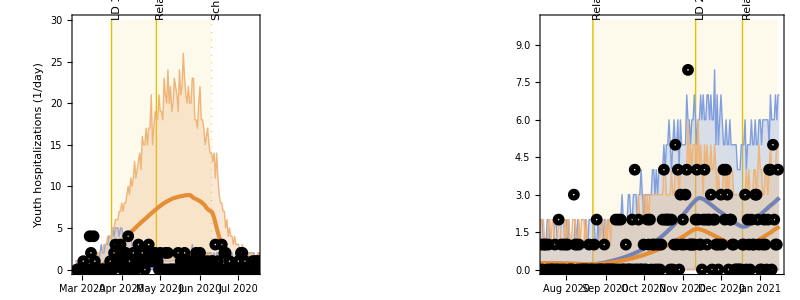

```mathematica
(* Plotting *)
(* Scatter plot for the hospitalization data *)scatterPlotHospData = DateListPlot[Total[hospitalizationData,{2}], "February 26, 2020", Joined->False, PlotTheme -> "Web",PlotMarkers->{Graphics[{Black,Style[Circle[],Thickness[0.25]]}],5}];
scatterPlotHospDataChild = DateListPlot[Total[hospitalizationData[[All, 1;;3]],{2}], "February 26, 2020", Joined->False, PlotTheme -> "Web",PlotMarkers->{Graphics[{Black,Style[Circle[],Thickness[0.25]]}],5}];

(* For hospitalizations, we use the median of the solutions (not noised) and the quantiles of the simulated (noised) *)hospSimulTotal2Plot = {hospitalizationSimulatedScenariosTotal[[1,1, All, All]],
hospitalizationSimulatedScenariosTotal[[2,1, All, All]],
hospitalizationSimulatedScenariosTotal[[3,1, All, All]]};
hospTot2Plot = {hospitalizationScenariosTotal[[1,1, All, All]],
hospitalizationScenariosTotal[[2,1, All, All]],
hospitalizationScenariosTotal[[3,1, All, All]]};
hospSimulYouth2Plot = {hospitalizationSimulatedScenariosGrouped[[1,1, All, All]],
hospitalizationSimulatedScenariosGrouped[[2,1, All, All]],
hospitalizationSimulatedScenariosGrouped[[3,1, All, All]]};
hospYouth2Plot={hospitalizationScenariosGrouped[[1,1, All, All]],
hospitalizationScenariosGrouped[[2,1, All, All]],
hospitalizationScenariosGrouped[[3,1, All, All]]};

figHospTotal = plotScenarioTrajectories[hospSimulTotal2Plot, "Total hospitalizations (1/day)",{"Scenario 1\nSchools remained open","Scenario 2\nSchools remained closed"},{ticksInvisible, ticksInvisible},{{0,590},{0,360}},{"a", "c"}, "lefter",scatterPlotHospData, 
hospTot2Plot];
figHospYouth = plotScenarioTrajectories[hospSimulYouth2Plot, "Youth hospitalizations (1/day)",{"", ""},{ticksVisible, ticksVisible},{{0,30},{0,10}},{"b", "d"}, "lefter",scatterPlotHospDataChild, 
hospYouth2Plot];


figHospTotalYouth = Grid[{{figHospTotal}, {figHospYouth}}];
exportFigs[figHospTotalYouth, "Fig2"];
```

### Seroprevalence

```mathematica
(* Susceptible population for the 10 age groups, for youth and adults, and for the total population *)susceptibleScenarios =importExport4Trajectories[varsS, "SUSCEPTIBLE"];
susceptibleScenariosGrouped = summingGroups4Scenarios[susceptibleScenarios, groupIndex];
susceptibleScenariosTotal = summingGroups4Scenarios[susceptibleScenarios, {Range[1, 10]}];

(* Calculating the seroprevalence for the total population *)
seroprevalenceScenariosTotal = 100-100susceptibleScenariosTotal/Total[demographyData10];
(* for youth and adults *)
seroprevalenceScenariosGrouped = ConstantArray[0, {3,2,100,327}];
Table[seroprevalenceScenariosGrouped[[All, k, All, All]]=
100-100susceptibleScenariosGrouped[[All,k,All,All]]/Total[demographyData10[[groupIndex[[k]]]]];, {k ,1,2}];
(* and for the 10 age groups *)
seroprevalenceScenarios = ConstantArray[0, {3,10,100,327}];
Table[seroprevalenceScenarios[[All, k, All, All]]=
100-100susceptibleScenarios[[All,k,All,All]]/Total[demographyData10[[k]]];, {k ,1,numAgeGroups}];
```

```mathematica
(* Assuming that the susceptible population is proportional to the total population, the [1,5) population percentage can be computed as follows *)susceptible1to5Percent = Total[demographyData85[[2;;5]]]/Total[demographyData85[[1;;5]]];
susceptibleScenariosWithoutBabies = susceptibleScenarios;
susceptibleScenariosWithoutBabies[[All,1,All,All]]=susceptible1to5Percent*susceptibleScenarios[[All,1,All,All]];
demographyData10WithoutBabies = demographyData10;
demographyData10WithoutBabies[[1]] =susceptible1to5Percent* demographyData10[[1]];

regroupIndex = {{1,2}, {3},{4,5}, {6,7}, {8,9,10}};
susceptibleScenariosRegrouped4Sero = summingGroups4Scenarios[susceptibleScenariosWithoutBabies,regroupIndex ];
seroprevalenceScenariosRegrouped = ConstantArray[0, {3,5,100,327}];
Table[seroprevalenceScenariosRegrouped[[All, k, All, All]]=
100-100susceptibleScenariosRegrouped4Sero[[All,k,All,All]]/Total[demographyData10WithoutBabies[[regroupIndex[[k]]]]];, {k ,1,5}];
```

### Contacts

```mathematica
(* Evaluating the contact expressions *)
trajectoriesContacts[i_, t_, sample_]:=Table[Table[contactMatrixWhich[scenarios[[i]],t]/.parametersCompleteSampled⟦sample⟧/.contactRates, {l, 1, numAgeGroups}], {k, 1, numAgeGroups}];
importExport4Contacts[label_] := Module[{func},
func[i_] := Table[Table[trajectoriesContacts[i, t, j],{t,tStart,tEnd,tStep}],{j,1,Length[listSamples]}];
importExportScenarioResults[label, func, "solutions"]];
(* and saving them as CONTACT files (these are still contact matrices) *)
contactMatricesScenarios = importExport4Contacts["CONTACTS"];
```

```mathematica
(* Getting the average contacts *)
demographyData1010 =Transpose[Table[demographyData10, {i, 1, numAgeGroups}]];
averageContactMatrixTotalScenarios = contactMatricesScenarios;
Do[averageContactMatrixTotalScenarios[[i,j,k,All,All]]=contactMatricesScenarios[[i,j,k,All,All]]*demographyData1010,{i,1,numScenarios},{j,1,numSamples},{k,1,numTimes}];

averageContactsTotalScenarios = Total[averageContactMatrixTotalScenarios, {5}] / Total[demographyData10];
averageContactsTotalScenariosFunc[i_]:=averageContactsTotalScenarios[[i,All,All,All]];

importExportScenarioResults["CONTACTS_AVERAGE", averageContactsTotalScenariosFunc, "solutions"];

(* Getting the average contacts for total, and age-specific groups *)
averageContactsTotal= Total[averageContactsTotalScenarios[[All, All, All, Range[1,10]]], {4}];
averageContactsYouth= Total[averageContactsTotalScenarios[[All, All, All, Range[1,3]]], {4}];
averageContactsAdults =Total[averageContactsTotalScenarios[[All, All, All, Range[4,10]]], {4}];
```

### Reproduction number

```mathematica
(* The next generation matrix for each scenario *)NGM= Table[Table[((-1/D[eqsList[scenarios[[i]]]⟦p,2⟧,varsList⟦p⟧] D[eqsList[scenarios[[i]]]⟦k,2⟧,varsList⟦p⟧])),{k,eqNumbersExposed},{p,eqNumbersInfectious}], {i, 1, Length[scenarios]}];

(* Substituting values to the next generation matrices *)
substituteNGM[scenNum_, sample_, time_] :=
((NGM[[scenNum]]/. (First@solutionsScenarios[[scenNum]][[sample]])[[eqNumbersSusceptible]]) /. parametersCompleteSampled[[sample]]) /. t -> time;
NGMForLoop[i_] :=Table[Table[substituteNGM[i, j, t], {t,tStart,tEnd,tStep}],{j,1,Length[listSamples]}];
NGMScenarios = importExportScenarioResults["NGM", NGMForLoop, "analysis"];
```

```mathematica
(* Obtaining the reproduction number and the respective eigenvectors *)
eigenAllFirst[matrix_] := Module[{valRight, valLeft}, 
valRight = Eigensystem[matrix, 1];
valLeft = Eigensystem[Transpose[matrix], 1]; 
{valRight[[1]][[1]], 
valRight[[2]][[1]],
valLeft[[2]][[1]]}];
RtForLoop[i_] :=Table[Table[eigenAllFirst[NGMScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];
RtScenarios = importExportScenarioResults["EIGEN", RtForLoop, "analysis"];
```

### Cumulative elasticities

```mathematica
(* The remaining analyses are done numerically (and not symbolically) *)
(* Sensitivity matrices *)
sensMatrix[eigen_]:=
Module[{eigenRight, eigenLeft},
eigenRight = eigen[[2]];
eigenLeft = eigen[[3]];Outer[Times,eigenLeft,eigenRight]/Dot[eigenLeft, eigenRight]];
sensForLoop[i_] :=Table[Table[sensMatrix[RtScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];
sensScenarios = importExportScenarioResults["SENSITIVITY", sensForLoop, "analysis"];

(* Elasticity matrices *)
elasMatrix[eigen_, NGM_, sens_] := 
Module[{R},
R = eigen[[1]];
NGM * sens / R];
elasForLoop[i_] :=Table[Table[elasMatrix[RtScenarios[[i, j, t]], NGMScenarios[[i, j, t]], sensScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];
elasScenarios = importExportScenarioResults["ELASTICITY", elasForLoop, "analysis"];

(* Cumulative elasticities *)
cumuElasMatrix[elas_] :=
Total[elas,{1}];
cumuElasForLoop[i_] := Table[Table[cumuElasMatrix[elasScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];
cumuElasScenarios = importExportScenarioResults["CUMUELAS", cumuElasForLoop, "analysis"];

(* Adding cumulative elasticities for age-specific groups (youth and adults) *)
cumuElasGroupedScenarios = Table[Table[Total[cumuElasScenarios[[scen]][[sample]][[time]][[groupIndex[[i]]]]], {i, 1, Length[groupIndex]}], {scen, 1, Length[scenarios]}, {sample, 1, Length[listSamples]}, {time, 1, numTimes}];
```

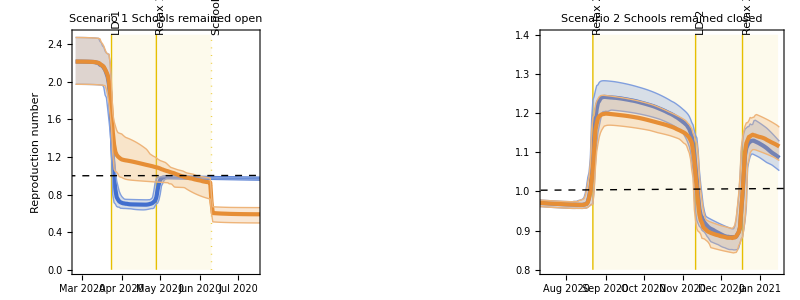
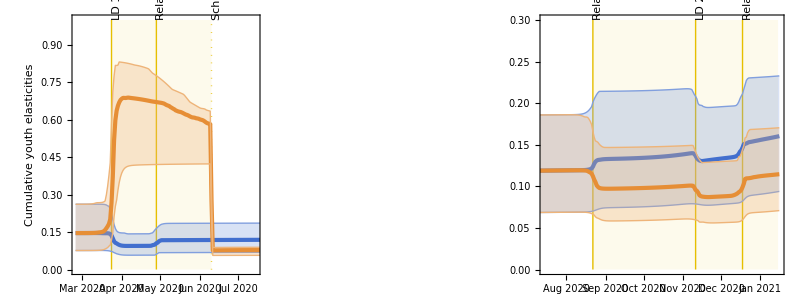

```mathematica
(* Plotting *)
Rt1Line = Graphics[{Dashed,Black,InfiniteLine[{AbsoluteTime["February 26, 2020"],1},{AbsoluteTime["January 15, 2020"],1}]}];

Rt2Plot ={RtScenarios[[1,All,All,1]],
RtScenarios[[2,All,All,1]],
RtScenarios[[3,All,All,1]]};
cumuElas2Plot = {cumuElasGroupedScenarios[[1,All,All,1]],
cumuElasGroupedScenarios[[2,All,All,1]],
cumuElasGroupedScenarios[[3,All,All,1]]};

figRt = plotScenarioTrajectories[Rt2Plot, "Reproduction number",{"Scenario 1\nSchools remained open","Scenario 2\nSchools remained closed"},{ticksInvisible, ticksInvisible},{{0,2.5},{0.8,1.4}}, {"a", "c"}, "righter", Rt1Line];
figCumuElas = plotScenarioTrajectories[cumuElas2Plot,"Cumulative youth elasticities",{"",""},{ticksVisible,ticksVisible},{{0,1},{0, 0.3}},{"b", "d"}, "righter"];

figRtCumuElasChild = Grid[{{figRt}, {figCumuElas}}];
exportFigs[figRtCumuElasChild, "Fig3"];
```

## Supplementary figures

### Contact matrices

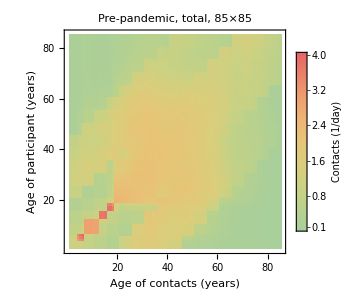
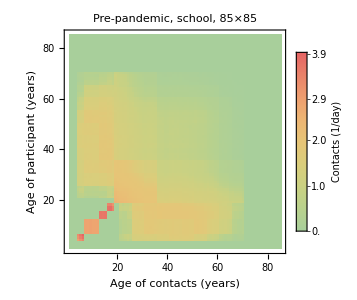
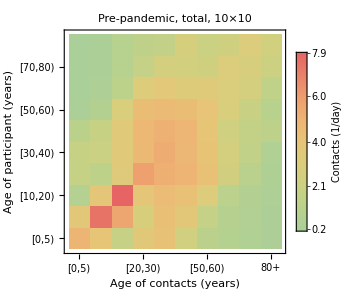
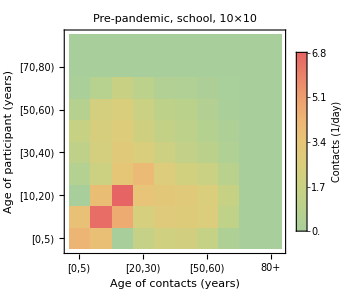
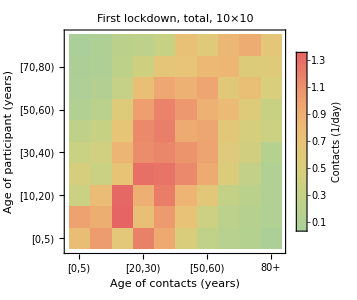
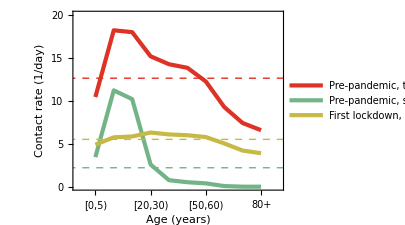
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
(* Plotting *)
mats2Plot={contactDataBefore85,schoolContactDataBefore85,contactDataBefore10,schoolContactDataBefore10,contactDataAfter10};
matTitles = {"Pre-pandemic, total, 85×85", "Pre-pandemic, school, 85×85", "Pre-pandemic, total, 10×10", "Pre-pandemic, school, 10×10",
"First lockdown, total, 10×10"};
figMats=Table[plotWithLetter[plotMatrix[mats2Plot[[matIndex]],"Rainbow",matTitles[[matIndex]],"contact"],alphabetLetters[[matIndex]]],{matIndex,1,Length[mats2Plot]}];
figF=plotWithLetter[plotThickLine[{calculateContactsAgeGroupsBefore,calculateSchoolContactsAgeGroupsBefore,calculateContactsAgeGroupsAfter},{colorRed,colorGreen,colorYellow},"","Age (years)","Contact rate (1/day)",{"Pre-pandemic, total","Pre-pandemic, schools","First lockdown, total"},"contacts",{calculateAverageContactRateBefore,calculateAverageContactRateSchoolsBefore,calculateAverageContactRateAfter},{{0,11},{0,20}},ImagePadding->{{41,Automatic},{Automatic,Automatic}}],"F"];

figConts=Grid[{{figMats[[1]],figMats[[2]]},{figMats[[3]],figMats[[4]]},{figMats[[5]],figF}}];
exportFigs[figConts, "SFig1"];
```

### Contact patterns

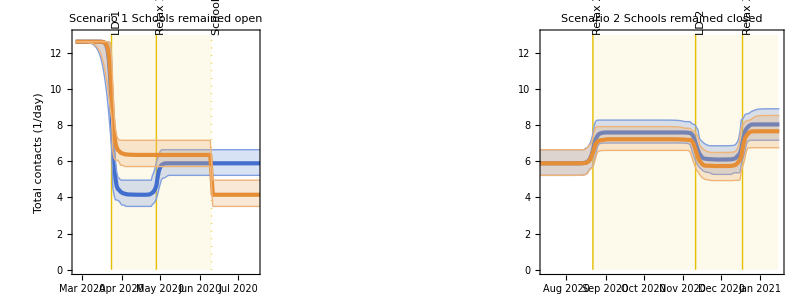
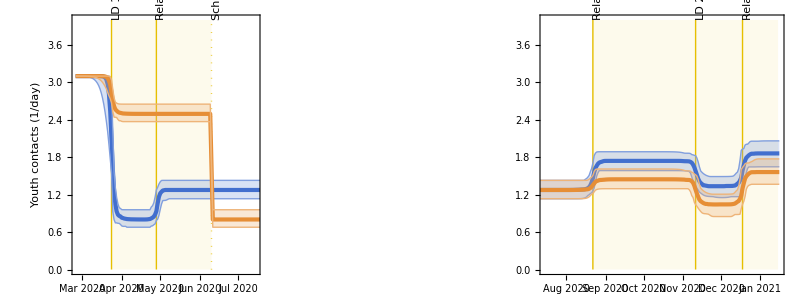
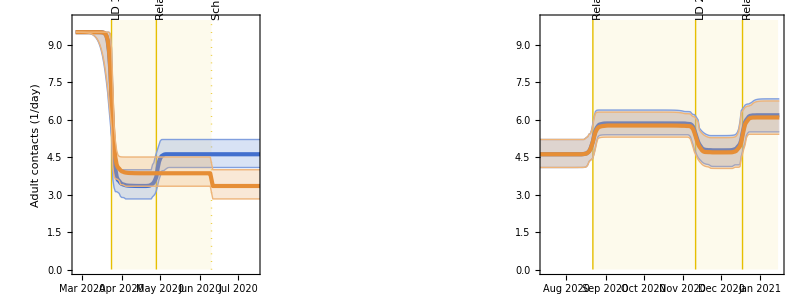

```mathematica
(* Plotting *)
aveContsTotal2Plot = {averageContactsTotal[[1,All,All]],
averageContactsTotal[[2,All,All]],
averageContactsTotal[[3,All,All]]};
aveContsYouth2Plot  ={averageContactsYouth[[1,All,All]],
averageContactsYouth[[2,All,All]],
averageContactsYouth[[3,All,All]]};
aveContsAdults2Plot ={averageContactsAdults[[1,All,All]],
averageContactsAdults[[2,All,All]],
averageContactsAdults[[3,All,All]]};

figContsTotal= plotScenarioTrajectories[aveContsTotal2Plot,"Total contacts (1/day)",{"Scenario 1\nSchools remained open","Scenario 2\nSchools remained closed"},{ticksInvisible,ticksInvisible},{{0,13},{0,13}},{"a", "b"}, "righter"];
figContsYouth= plotScenarioTrajectories[aveContsYouth2Plot,"Youth contacts (1/day)",{"",""},{ticksInvisible,ticksInvisible},{{0,4},{0,4}}, {"c", "d"}, "righter"];
figContsAdults= plotScenarioTrajectories[aveContsAdults2Plot,"Adult contacts (1/day)",{"",""},{ticksVisible,ticksVisible},{{0,10},{0,10}}, {"e", "f"}, "righter"];

figContsTotalAges = Grid[{{figContsTotal},{figContsYouth}, {figContsAdults}}];
exportFigs[figContsTotalAges, "SFig2"];
```

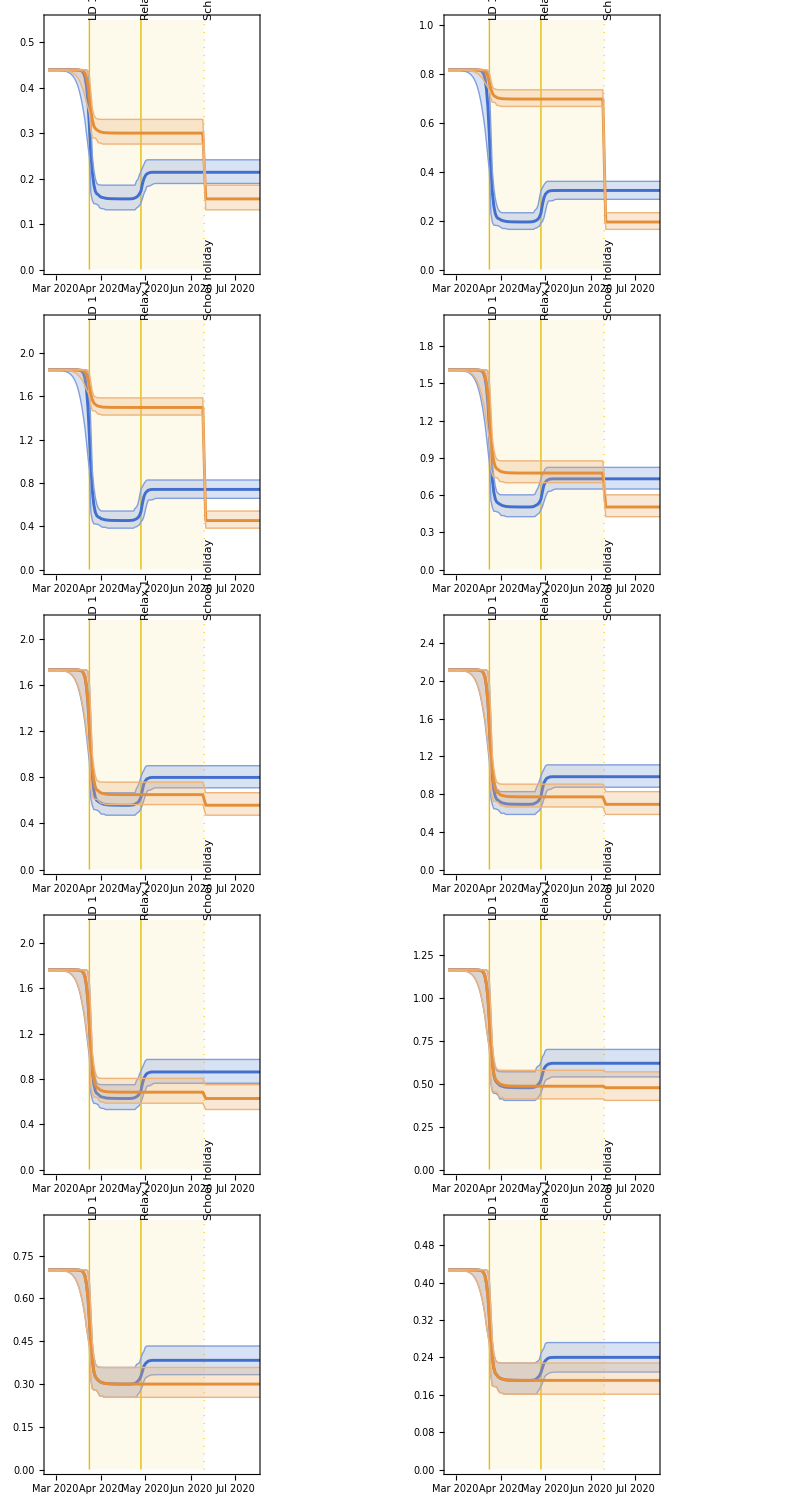
| Scenario 1
Schools remained open
Average contacts (1/day) | -Graphics-

```mathematica
figContacts10Scen1=Table[
Module[{maxVal, maxRange}, 
maxVal = Quantile[averageContactsTotalScenarios[[2, All, All, k]], 0.975];
maxRange = Max[maxVal] + Max[maxVal]/4;
plotWithLetter[{plotLineWithCrI[averageContactsTotalScenarios[[1, All, All, k]],colorBlue,"","","",1,If[k>8,ticksVisible, ticksInvisible],{0, maxRange}, 0.5, 350],
plotLineWithCrI[averageContactsTotalScenarios[[2, All, All, k]],colorOrange]},ageLabelShort[[k]],"left", sizeFontBig, Black]], {k, 1, numAgeGroups}];

figContacts10Scen1 = Grid[{{"", Style["Scenario 1\nSchools remained open",TextAlignment -> Center,Black,sizeFontBig, FontFamily->"Helvetica"]},{Style[Rotate["Average contacts (1/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figContacts10Scen1, {5,2}]]}}];
exportFigs[figContacts10Scen1, "SFig3"];
```

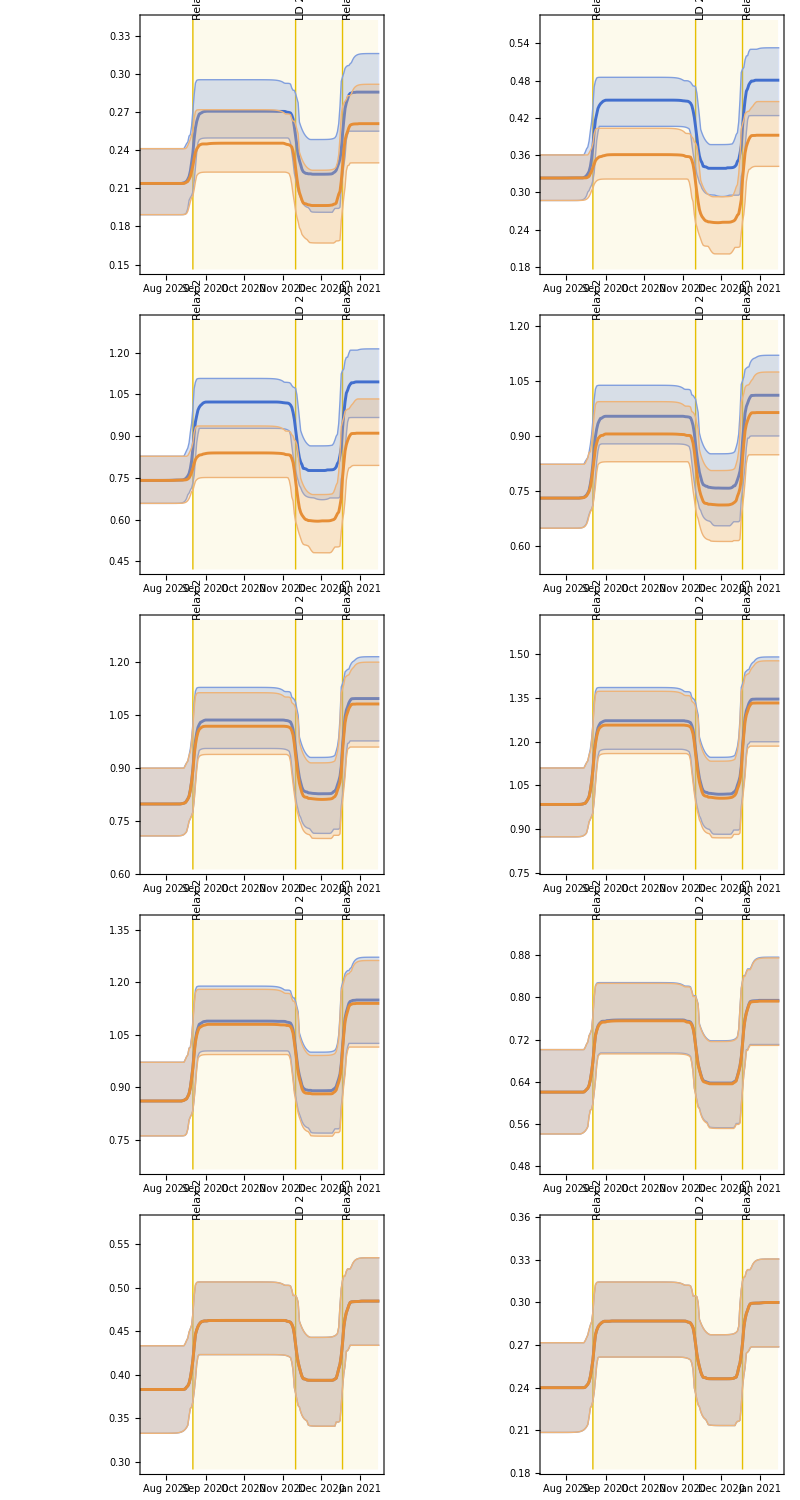
| Scenario 2
Schools remained closed
Average contacts (1/day) | -Graphics-

```mathematica
figContacts10Scen2=Table[
Module[{maxVal,minVal, minRange, maxRange}, 
maxVal = Quantile[averageContactsTotalScenarios[[1, All, Range[150, 300], k]], 0.975];
minVal = Quantile[averageContactsTotalScenarios[[3, All, Range[150, 300], k]], 0.025];
maxRange = Max[maxVal] + Max[maxVal]/8;
minRange = Min[minVal] - Min[minVal]/8;
plotWithLetter[{plotLineWithCrI[averageContactsTotalScenarios[[1, All, All, k]],colorBlue,"","","",2,If[k>8,ticksVisible, ticksInvisible],{minRange, maxRange}, 0.5, 350],
plotLineWithCrI[averageContactsTotalScenarios[[3, All, All, k]],colorOrange]},ageLabelShort[[k]],"left", sizeFontBig, Black]], {k, 1, numAgeGroups}];

figContacts10Scen2 = Grid[{{"", Style["Scenario 2\nSchools remained closed",TextAlignment -> Center,Black,sizeFontBig, FontFamily->"Helvetica"]},{Style[Rotate["Average contacts (1/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figContacts10Scen2, {5,2}]]}}];
exportFigs[figContacts10Scen2, "SFig4"];
```

### Estimated parameters

i::shdw: Symbol i appears in multiple contexts {plotting`,preliminaries`}; definitions in context plotting` may shadow or be shadowed by other definitions.

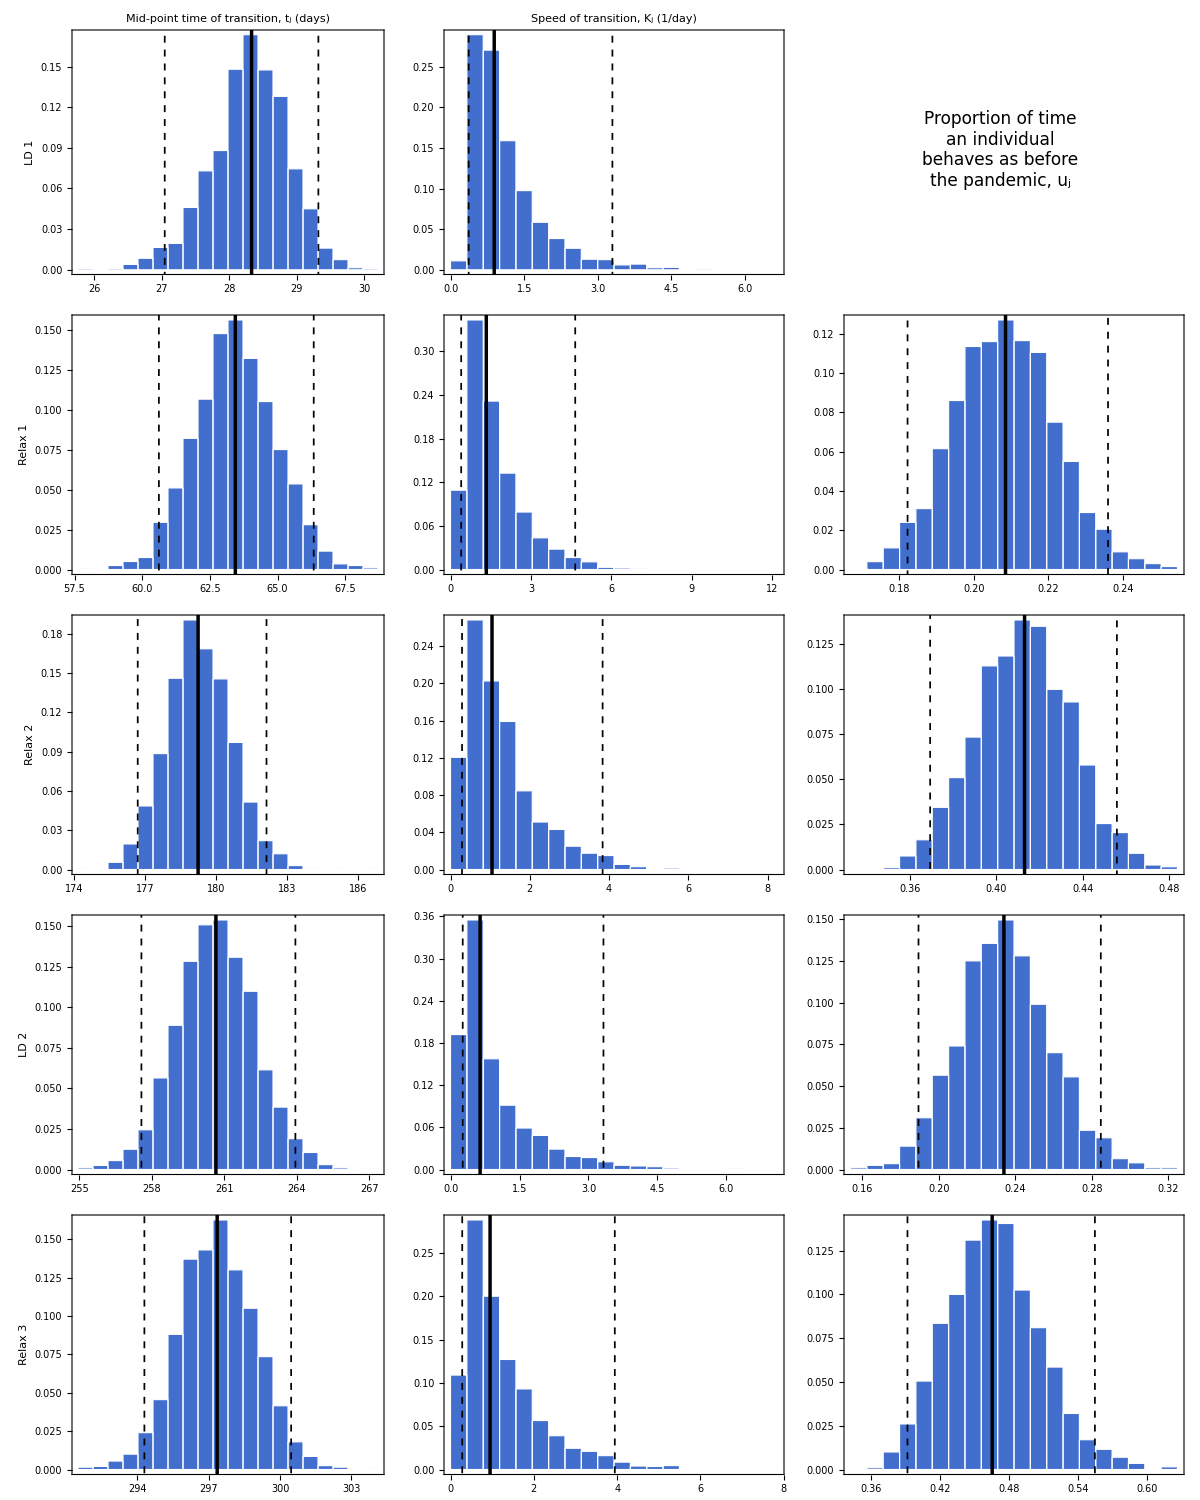

```mathematica
(* Plotting contact-related parameters *)
Remove["plotting`*"]
Get["../packages/plotting.m"]

parameterTVals = {estimatesData⟦All,20⟧,estimatesData⟦All,22⟧,estimatesData⟦All,24⟧,estimatesData⟦All,26⟧,estimatesData⟦All,28⟧};
parameterKVals = {estimatesData⟦All,21⟧,estimatesData⟦All,23⟧,estimatesData⟦All,25⟧,estimatesData⟦All,27⟧,estimatesData⟦All,29⟧};
parameterUVals = {estimatesData⟦All,30⟧,estimatesData⟦All,31⟧,estimatesData⟦All,32⟧,estimatesData⟦All,33⟧};

figT = Table[plotWithLetter[plotHistogram[parameterTVals[[i]], If[i == 1, Style["Mid-point time of transition, \nt_j (days)"], ""],
"", Style[transitionDatesLabelsShort[[i]]], colorBlue], parameterTXLabel[[i]], "right", sizeFontBig],{i, 1, Length[parameterTVals]}];
figK = Table[plotWithLetter[
{plotHistogram[parameterKVals[[i]], If[i == 1, Style["Speed of transition, \nK_j (1/day)"], ""],"",  "", colorBlue]}, parameterKXLabel[[i]], "right", sizeFontBig],{i, 1, Length[parameterKVals]}];
figU = Table[plotWithLetter[
{plotHistogram[parameterUVals[[i]], "", "",  "", colorBlue,
If[i == 2, {0.33, 0.49},True]]}, parameterUXLabel[[i]], "right", sizeFontBig],{i, 1, Length[parameterUVals]}];
figU = Prepend[figU,Graphics[Text[Style["Proportion of time\nan individual\nbehaves as before\nthe pandemic, u_j\n\n\n\n", sizeFontBig]]]];

figContParams = Grid[Transpose[{figT, figK, figU}]];
exportFigs[figContParams, "SFig5"];
```

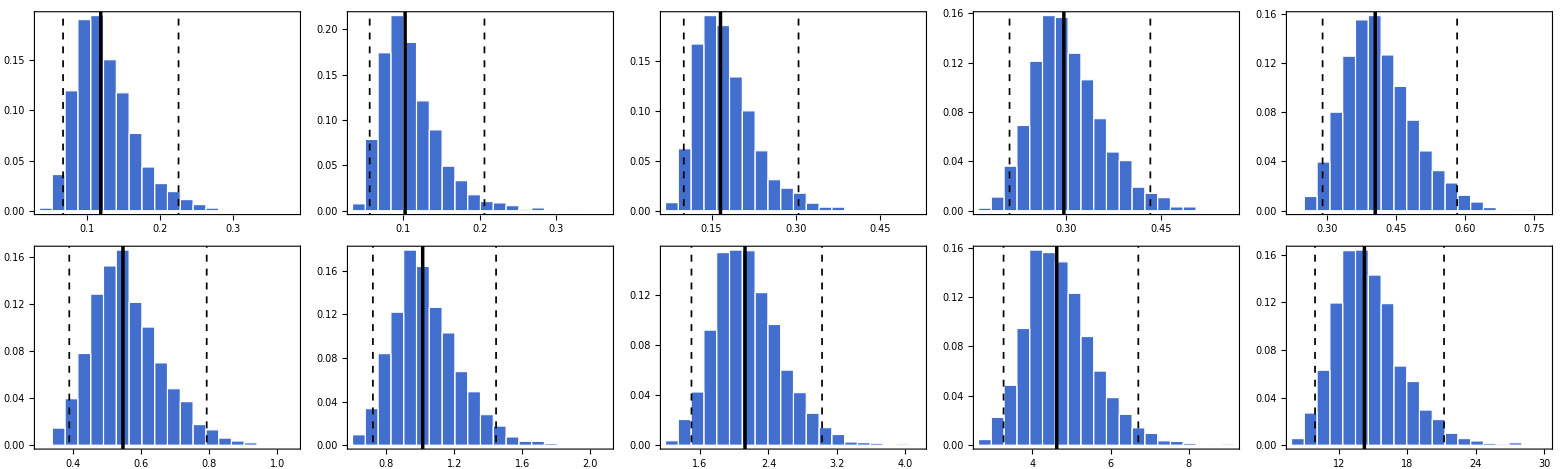
| Hospitalization rates, ν_k (1/day)
Probability | -Graphics-

```mathematica
(* Plotting hospitalization rates *)
parameterHospRateVals = Table[365 estimatesData⟦All,2+i⟧,{i,1,numAgeGroups}];

figHospRates = Table[plotWithLetter[
{plotHistogram[parameterHospRateVals[[i]], "","",  "", colorBlue,
Which[i == 1,{0.04, 0.27},i == 2,{0.02, 0.29},True, True]]}, ageLabelShort[[i]], Scaled[{0.85, 0.9}], sizeFontBig, Black],{i, 1, Length[parameterHospRateVals]}];

figHospRates = Grid[{{"", Style[Rotate["Hospitalization rates, ν_k (1/day)",0],Black,sizeFontBig, FontFamily->"Helvetica"]},{Style[Rotate["Probability",Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"], Grid[ArrayReshape[figHospRates, {2,5}]]}}];
exportFigs[figHospRates, "SFig6"];
```

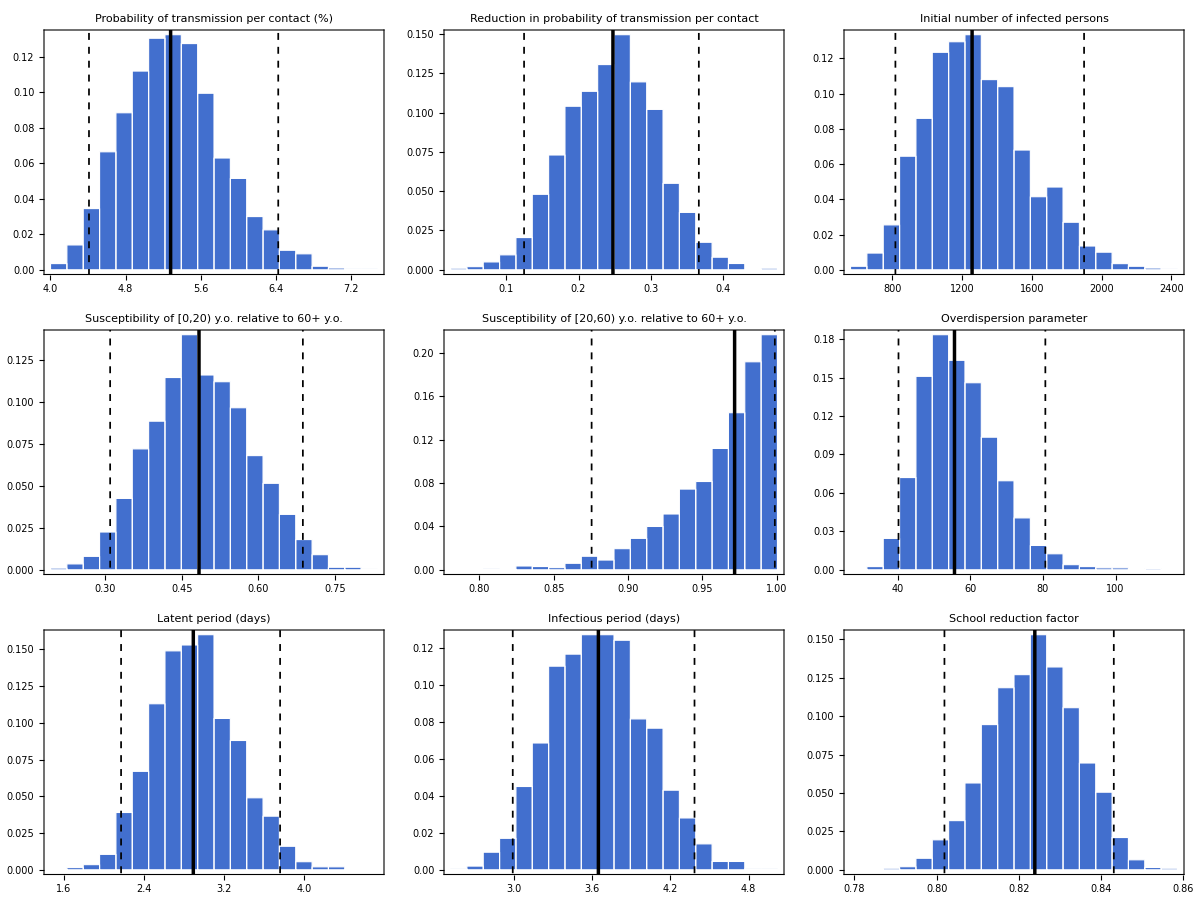
Probability | -Graphics-

```mathematica
(* Plotting all the other remaining parameters *)
parameterConstVals = {estimatesData⟦All,1⟧ 100,1-estimatesData⟦All,2⟧,estimatesData⟦All,13⟧ Total[demographyData10],estimatesData⟦All,14⟧,estimatesData⟦All,15⟧,estimatesData⟦All,17⟧,1/estimatesData⟦All,18⟧,1/estimatesData⟦All,19⟧};

figConstsTables = Table[plotWithLetter[plotHistogram[parameterConstVals[[i]], Style[parameterConstXLabel[[i]]],
"","", colorBlue], parameterConstXLabelShort[[i]], Which[i ==3, Scaled[{0.8, 0.9}], i == 5, Scaled[{0.2, 0.9}],True, "right"], sizeFontBig],{i, 1, Length[parameterConstVals]}];
figSRF = plotWithLetter[plotHistogram[1-schRedFacObtained, Style["\nSchool reduction factor"],
"", "", colorBlue],"1-ζ_s", "right", sizeFontBig];
figConstsParams = Grid[{{Style[Rotate["Probability",Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"], Grid[ArrayReshape[{figConstsTables, figSRF}, {3,3}]]}}];

exportFigs[figConstsParams, "SFig7"];
```

### Model fit to seroprevalence data

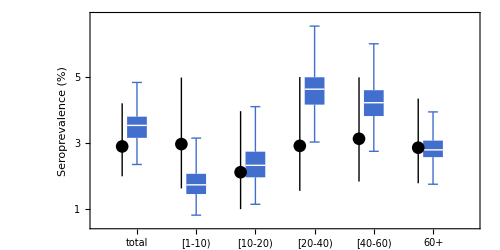

```mathematica
(* Plotting *)
seroEstimatesMay28 = {seroprevalenceScenariosTotal[[1,1,All,93]],seroprevalenceScenariosRegrouped[[1, 1, All, 93]], seroprevalenceScenariosRegrouped[[1, 2, All, 93]], seroprevalenceScenariosRegrouped[[1, 3, All, 93]], seroprevalenceScenariosRegrouped[[1, 4, All, 93]], seroprevalenceScenariosRegrouped[[1, 5, All, 93]]};

figSeroDataEstimate = Show[{plotBoxWhisker[seroEstimatesMay28, {colorBlue}, {"total", "[1-10)", "[10-20)", "[20-40)", "[40-60)", "60+"},
"", "Seroprevalence (%)"],
ListPlot[Transpose[{Range[6]-0.25,seroDataMay28Around}], PlotMarkers->{Automatic, 13},PlotStyle -> Black, IntervalMarkers -> "Fences", IntervalMarkersStyle -> {Black, Thick}]}];
exportFigs[figSeroDataEstimate, "SFig8"];
```

### Model fit to hospitalization data

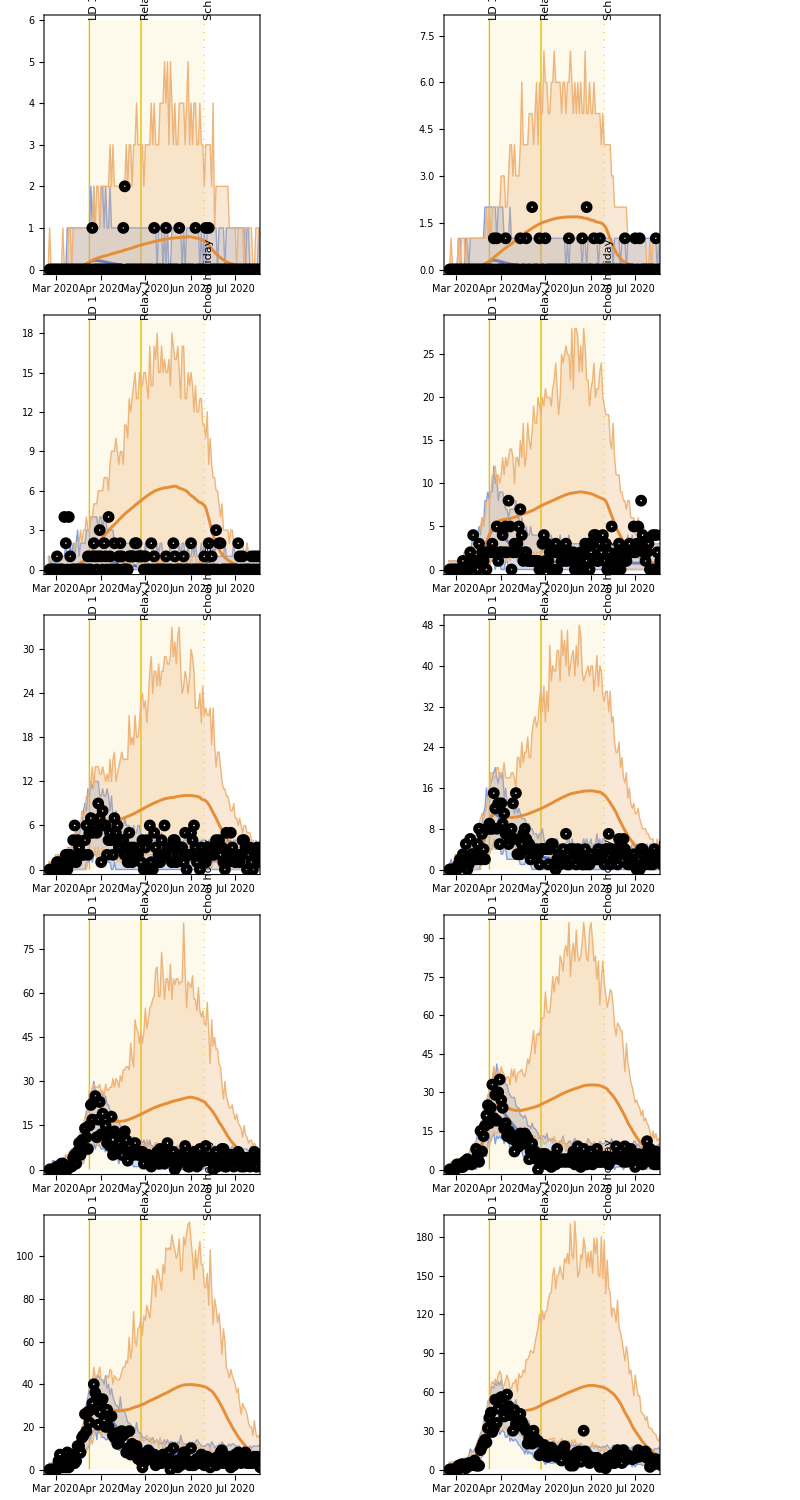
| Scenario 1
Schools remained open
Hospitalizations (1/day) | -Graphics-

```mathematica
scatterPlotHospData10Groups[k_] := DateListPlot[hospitalizationData[[All,k]], "February 26, 2020", Joined->False, PlotTheme -> "Web",PlotMarkers->{Graphics[{Black,Style[Circle[],Thickness[0.25]]}],5}];

figHosp10Scen1=Table[
Module[{maxVal, maxRange}, 
maxVal = Quantile[hospitalizationSimulatedScenarios[[2, k, All, All]], 0.975];
maxRange = Max[maxVal]+1;
plotWithLetter[{plotLineWithCrI[hospitalizationSimulatedScenarios[[1, k, All, All]],colorBlue,"","","",1,If[k>8,ticksVisible, ticksInvisible],{0, maxRange}, 0.5, 350, Solid, hospitalizationScenarios[[1,k,All,All]]],
plotLineWithCrI[hospitalizationSimulatedScenarios[[2, k, All, All]],colorOrange,"","","",1,If[k>8,ticksVisible, ticksInvisible],{0, maxRange}, 0.5, 350, Solid, hospitalizationScenarios[[2,k,All,All]]],
scatterPlotHospData10Groups[k]},ageLabelShort[[k]],"left", sizeFontBig, Black]], {k, 1, numAgeGroups}];

figHosp10Scen1 = Grid[{{"", Style["Scenario 1\nSchools remained open",TextAlignment -> Center,Black,sizeFontBig, FontFamily->"Helvetica"]},{Style[Rotate["Hospitalizations (1/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figHosp10Scen1, {5,2}]]}}];
exportFigs[figHosp10Scen1, "SFig9"];
```

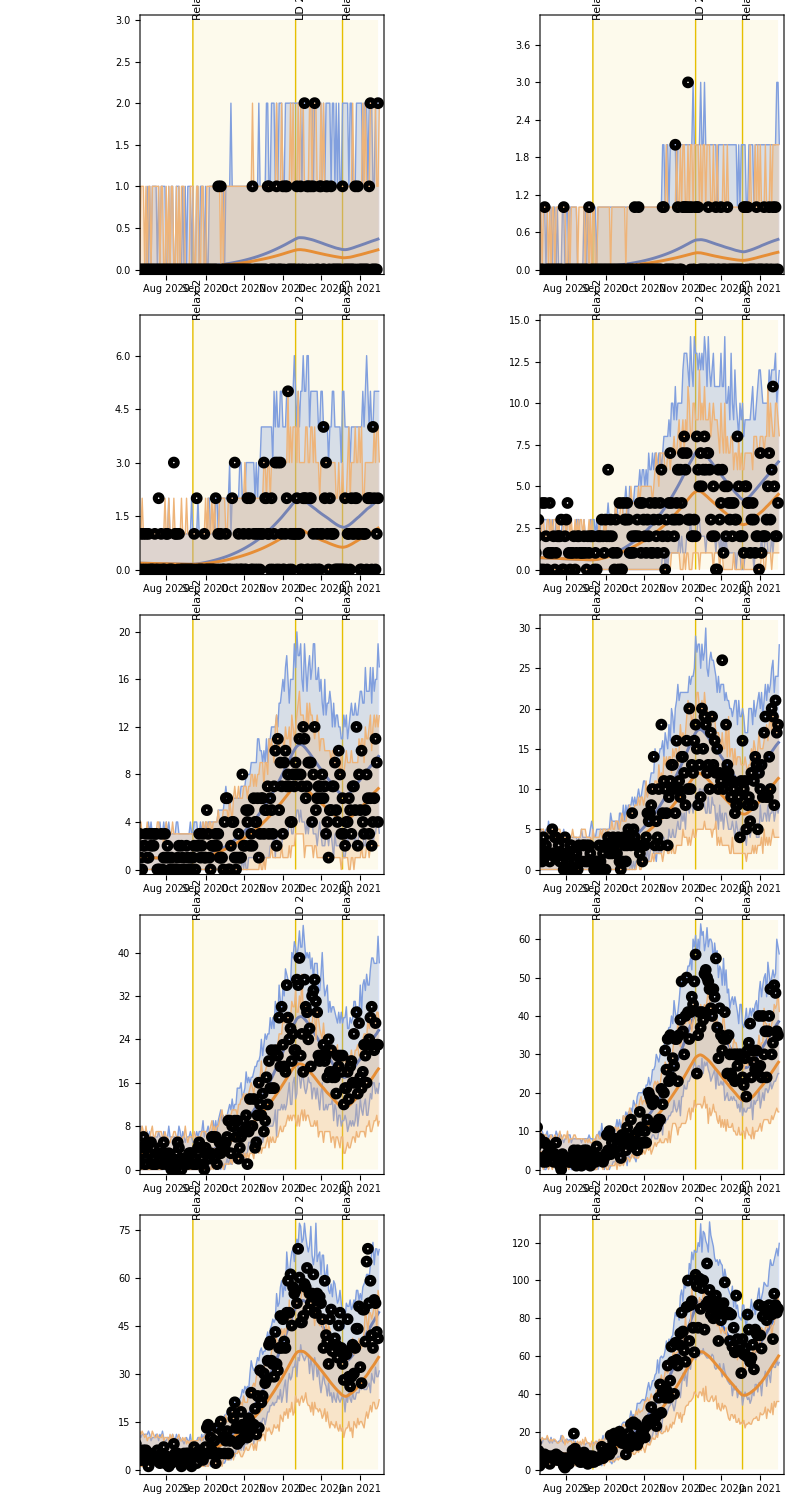
| Scenario 2
Schools remained closed
Hospitalizations (1/day) | -Graphics-

```mathematica
figHosp10Scen2=Table[
Module[{maxVal, maxRange}, 
maxVal = Quantile[hospitalizationSimulatedScenarios[[1, k, All, All]], 0.975];
maxRange = Max[maxVal]+1;
plotWithLetter[{plotLineWithCrI[hospitalizationSimulatedScenarios[[1, k, All, All]],colorBlue,"","","",2,If[k>8,ticksVisible, ticksInvisible],{0, maxRange}, 0.5, 350, Solid, hospitalizationScenarios[[1,k,All,All]]],
plotLineWithCrI[hospitalizationSimulatedScenarios[[3, k, All, All]],colorOrange,"","","",2,If[k>8,ticksVisible, ticksInvisible],{0, maxRange}, 0.5, 350, Solid, hospitalizationScenarios[[3,k,All,All]]],
scatterPlotHospData10Groups[k]},ageLabelShort[[k]],"left", sizeFontBig, Black]], {k, 1, numAgeGroups}];

figHosp10Scen2 = Grid[{{"", Style["Scenario 2\nSchools remained closed",TextAlignment -> Center,Black,sizeFontBig, FontFamily->"Helvetica"]},{Style[Rotate["Hospitalizations (1/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figHosp10Scen2, {5,2}]]}}];
exportFigs[figHosp10Scen2, "SFig10"];
```

### Age-specific contributions to R(t)

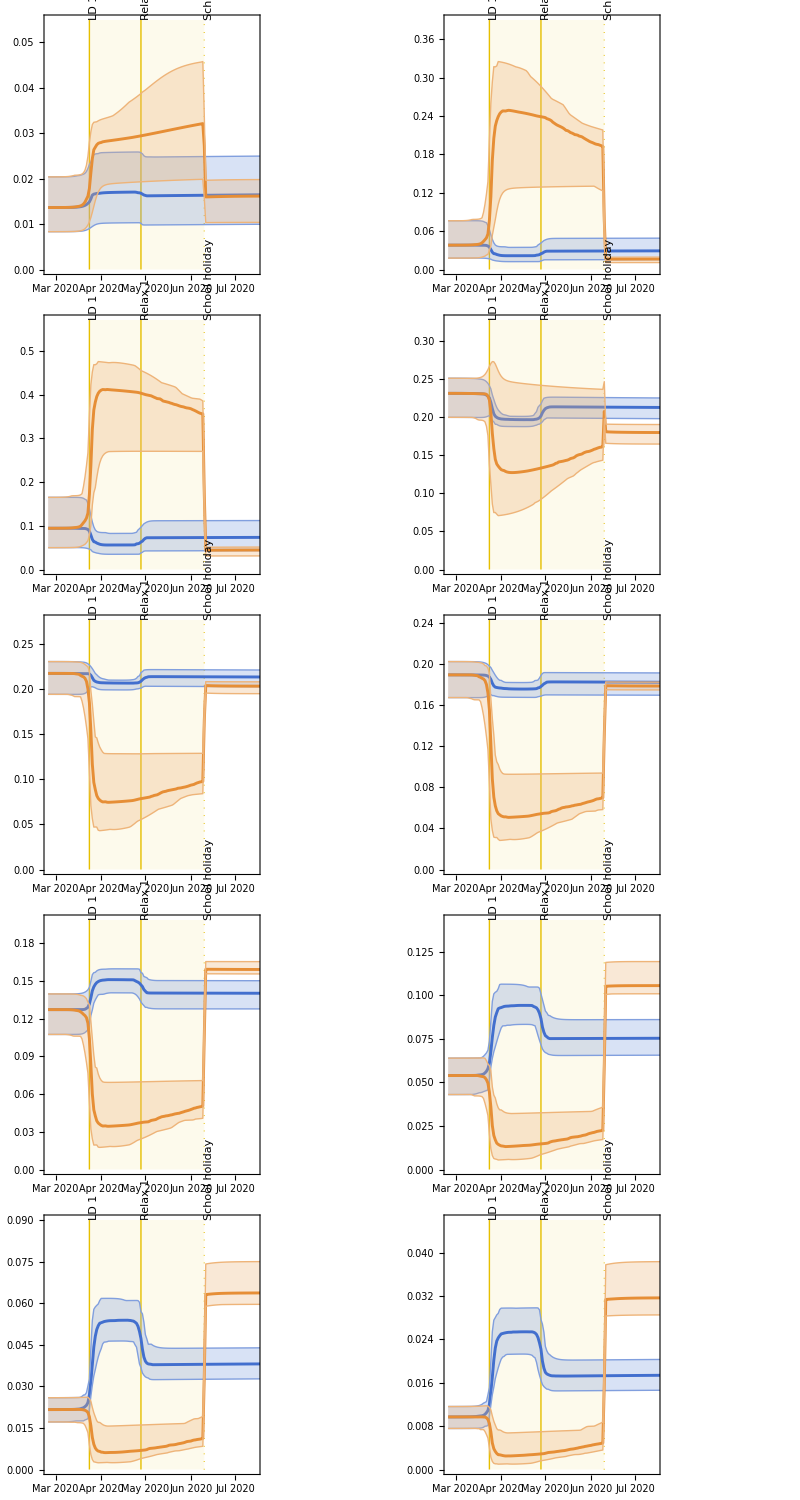
| Scenario 1
Schools remained open
Cumulative elasticities | -Graphics-

```mathematica
figCumuElas10Scen1=Table[
Module[{maxVal, maxRange}, 
maxVal = Quantile[cumuElasScenarios[[2, All, All, k]], 0.975];
maxRange = Max[maxVal]+Max[maxVal]/5;
plotWithLetter[{plotLineWithCrI[cumuElasScenarios[[1, All, All, k]],colorBlue,"","","",1,If[k>8,ticksVisible, ticksInvisible],{0, maxRange}, 0.5, 350],
plotLineWithCrI[cumuElasScenarios[[2, All, All, k]],colorOrange]},ageLabelShort[[k]],"left", sizeFontBig,Black]], {k, 1, numAgeGroups}];

figCumuElas10Scen1 = Grid[{{"", Style["Scenario 1\nSchools remained open",TextAlignment -> Center,Black,sizeFontBig, FontFamily->"Helvetica"]},{Style[Rotate["Cumulative elasticities", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figCumuElas10Scen1, {5,2}]]}}];
exportFigs[figCumuElas10Scen1, "SFig11"];
```

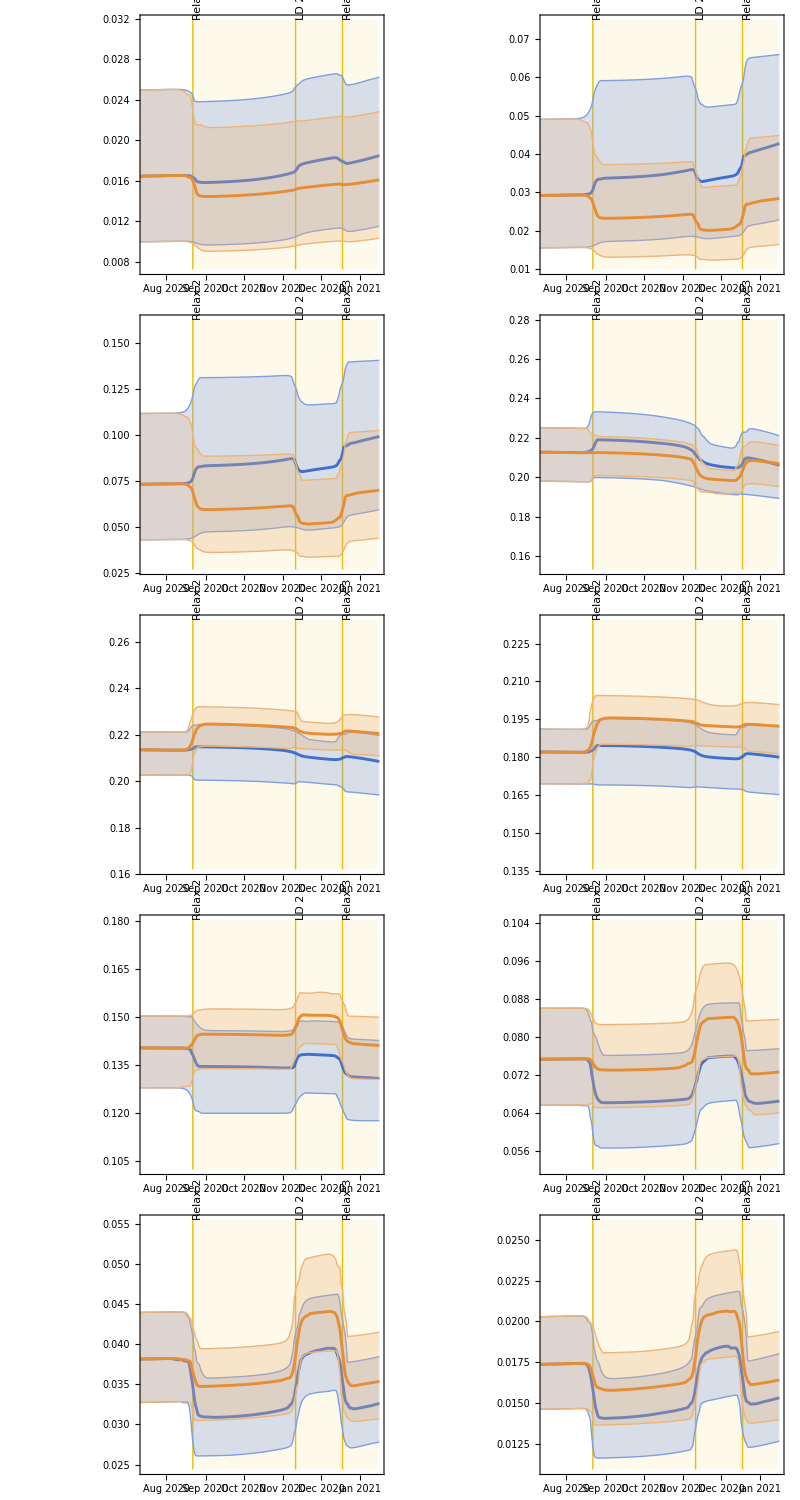
| Scenario 2
Schools remained closed
Cumulative elasticities | -Graphics-

```mathematica
figCumuElas10Scen2=Table[
Module[{maxVal,minVal,minRange, maxRange}, 
maxVal = Quantile[cumuElasScenarios[[1,All, Range[150,300], k]], 0.975];
minVal = Quantile[Re[cumuElasScenarios[[3, All,Range[150,300], k]]], 0.025];
maxRange = Min[1,Max[maxVal]+Max[maxVal]/5];
minRange = Max[0,Min[minVal]-Min[minVal]/5];
plotWithLetter[{plotLineWithCrI[cumuElasScenarios[[1, All, All, k]],colorBlue,"","","",2,If[k>8,ticksVisible, ticksInvisible],{minRange, maxRange}, 0.5, 350],
plotLineWithCrI[cumuElasScenarios[[3, All, All, k]],colorOrange]},ageLabelShort[[k]],"left", sizeFontBig,Black]], {k, 1, numAgeGroups}];

figCumuElas10Scen2 = Grid[{{"", Style["Scenario 2\nSchools remained closed",TextAlignment -> Center,Black,sizeFontBig, FontFamily->"Helvetica"]},{Style[Rotate["Cumulative elasticities", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figCumuElas10Scen2, {5,2}]]}}];
exportFigs[figCumuElas10Scen2, "SFig12"];
```

### Comparison of cumulative hospitalizations

```mathematica
hospMatrices = {hospitalizationScenarios,hospitalizationScenariosGrouped,hospitalizationScenariosTotal,hospitalizationSimulatedScenarios, hospitalizationSimulatedScenariosGrouped, hospitalizationSimulatedScenariosTotal};

cumuHospFunc[matrix_] := Table[Accumulate[matrix[[ii,jj,kk]]],
{ii, 1,Dimensions[matrix][[1]]},
{jj, 1, Dimensions[matrix][[2]]},
{kk, 1, Dimensions[matrix][[3]]}];
cumuHospMatrices= Table[cumuHospFunc[hospMatrices[[qq]]], {qq, 1, 6}];
cumuHospMatricesSelectDates= Table[N[cumuHospMatrices[[qq, All, All, All, {141, 325}]]], {qq, 1, 6}];
cumuHospMatricesSelectDatesEach = Map[Map[ReplacePart[#,{2}->#[[2]]-#[[1]]]&,#,{3}]&,cumuHospMatricesSelectDates];

stats4AgesHosp = getStats4Hosp[cumuHospMatricesSelectDatesEach[[1]], cumuHospMatricesSelectDatesEach[[4]]];
stats4GroupedHosp = getStats4Hosp[cumuHospMatricesSelectDatesEach[[2]], cumuHospMatricesSelectDatesEach[[5]]];
stats4TotalHosp = getStats4Hosp[cumuHospMatricesSelectDatesEach[[3]], cumuHospMatricesSelectDatesEach[[6]]];

relChange4AgesHospScen1 = getRelChange4Hosp[cumuHospMatricesSelectDatesEach[[1]], cumuHospMatricesSelectDatesEach[[4]],1];
relChange4GroupedHospScen1 = getRelChange4Hosp[cumuHospMatricesSelectDatesEach[[2]], cumuHospMatricesSelectDatesEach[[5]],1];
relChange4TotalHospScen1 = getRelChange4Hosp[cumuHospMatricesSelectDatesEach[[3]], cumuHospMatricesSelectDatesEach[[6]],1];
relChange4AgesHospScen2 = getRelChange4Hosp[cumuHospMatricesSelectDatesEach[[1]], cumuHospMatricesSelectDatesEach[[4]],2];
relChange4GroupedHospScen2 = getRelChange4Hosp[cumuHospMatricesSelectDatesEach[[2]], cumuHospMatricesSelectDatesEach[[5]],2];
relChange4TotalHospScen2 = getRelChange4Hosp[cumuHospMatricesSelectDatesEach[[3]], cumuHospMatricesSelectDatesEach[[6]],2];
```

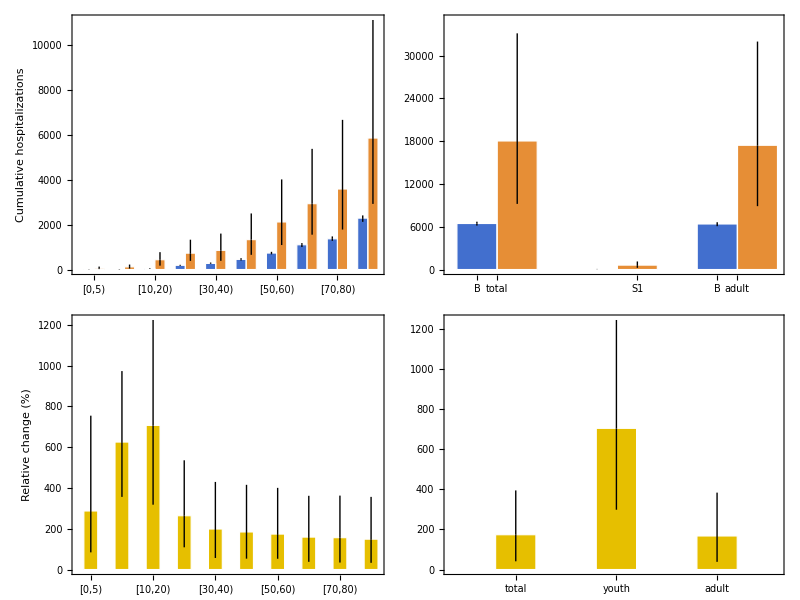

```mathematica
hospAbsScen1TotalGrouped = {{transformToAround[Ceiling[stats4TotalHosp[[All,1,1,1]]],0],
transformToAround[Ceiling[stats4TotalHosp[[All,2,1,1]]],0]},
{transformToAround[Ceiling[stats4GroupedHosp[[All,1,1,1]]],0],
transformToAround[Ceiling[stats4GroupedHosp[[All,2,1,1]]],0]},
{transformToAround[Ceiling[stats4GroupedHosp[[All,1,2,1]]],0],
transformToAround[Ceiling[stats4GroupedHosp[[All,2,2,1]]],0]}};
hospAbsScen1Ages = Transpose[Outer[transformToAround[Ceiling[stats4AgesHosp[[All,#1,#2,1]]], 0]&,{1,2},Range[1,10]]];


figHospScen1BarsAbsAges = plotWithLetter[
{plotBarWithError[hospAbsScen1Ages, {colorBlue, colorOrange}, {ageLabelShort, None}, "", "Cumulative hospitalizations", "", {0,Automatic}, 550, 250/550],
Graphics[{Inset[plotBarWithError[hospAbsScen1Ages[[1;;3]], {colorBlue, colorOrange}, {ageLabelShort, None}, "", "", "", {0,800}],
Scaled[{0.2, 0.55}], {Center, Center}, Scaled[0.6]]}]}, "a", "lefter"];

figHospScen1BarsAbsTot=plotWithLetter[
{plotBarWithError[hospAbsScen1TotalGrouped, {colorBlue, colorOrange}, {{"total", "youth", "adult"}, {"B", "S1"}}, "", "", "", {0,35000}, 400, 250/400],
Graphics[{Inset[plotBarWithError[hospAbsScen1TotalGrouped[[2]], {colorBlue, colorOrange}, {{"youth"}}, "", "", "", {0,1200}, 400, 250/400, {0.01, 1}, {0,3}],
Scaled[{0.47, 0.55}], {Center, Center}, Scaled[0.55]]}]},
"b", "lefter"];

figHospScen1BarsRelAges = plotWithLetter[
plotBarWithError[relChange4AgesHospScen1, colorYellowBright, ageLabelShort, "", "Relative change (%)", "", {0,Automatic},550, 250/550, 1.25], "c", "lefter"];

figHospScen1BarsRelTot= plotWithLetter[
plotBarWithError[
Flatten[{relChange4TotalHospScen1, relChange4GroupedHospScen1[[1]], relChange4GroupedHospScen1[[2]]}],
colorYellowBright, {"total", "youth", "adult"}, "", "", "", {0,Automatic},400, 250/400, 1.5],
"d", "lefter"];

figHospScen1Bars= Grid[{{figHospScen1BarsAbsAges,figHospScen1BarsAbsTot},
{figHospScen1BarsRelAges,figHospScen1BarsRelTot}}];
exportFigs[figHospScen1Bars, "SFig13"];
```

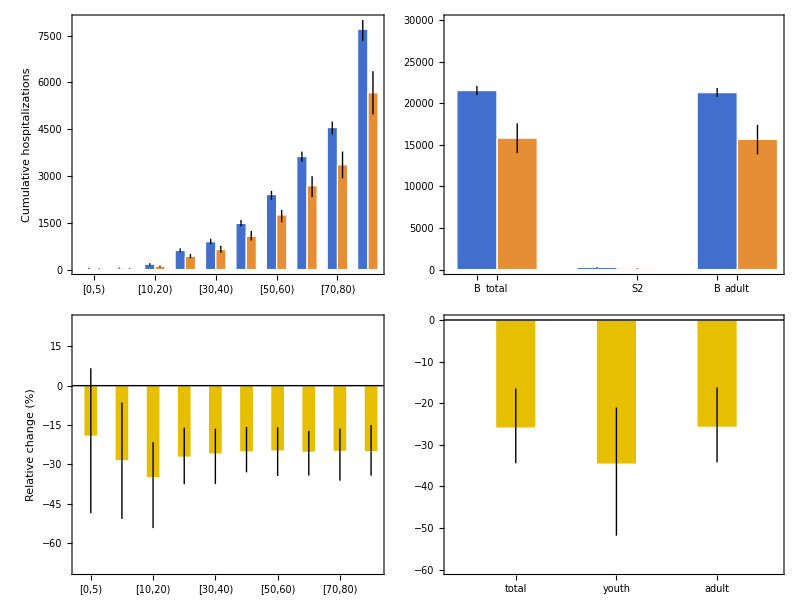

```mathematica
hospAbsScen2TotalGrouped = {{transformToAround[Ceiling[stats4TotalHosp[[All,1,1,2]]],0],
transformToAround[Ceiling[stats4TotalHosp[[All,3,1,2]]],0]},
{transformToAround[Ceiling[stats4GroupedHosp[[All,1,1,2]]],0],
transformToAround[Ceiling[stats4GroupedHosp[[All,3,1,2]]],0]},
{transformToAround[Ceiling[stats4GroupedHosp[[All,1,2,2]]],0],
transformToAround[Ceiling[stats4GroupedHosp[[All,3,2,2]]],0]}};
hospAbsScen2Ages = Transpose[Outer[transformToAround[Ceiling[stats4AgesHosp[[All,#1,#2,2]]], 0]&,{1,3},Range[1,10]]];

figHospScen2BarsAbsAges = plotWithLetter[
{plotBarWithError[hospAbsScen2Ages, {colorBlue, colorOrange}, {ageLabelShort, None}, "", "Cumulative hospitalizations", "", {0,Automatic}, 550, 250/550],
Graphics[{Inset[plotBarWithError[hospAbsScen2Ages[[1;;3]], {colorBlue, colorOrange}, {ageLabelShort, None}, "", "", "", {0,200}],
Scaled[{0.2, 0.55}], {Center, Center}, Scaled[0.6]]}]}, "a", "lefter"];

figHospScen2BarsAbsTot=plotWithLetter[
{plotBarWithError[hospAbsScen2TotalGrouped, {colorBlue, colorOrange}, {{"total", "youth", "adult"}, {"B", "S2"}}, "", "", "", {0,30000}, 400, 250/400],
Graphics[{Inset[plotBarWithError[hospAbsScen2TotalGrouped[[2]], {colorBlue, colorOrange}, {{"youth"}}, "", "", "", {0,300}, 400, 250/400, {0.01, 1}, {0,3}],
Scaled[{0.47, 0.55}], {Center, Center}, Scaled[0.55]]}]},
"b", "lefter"];

figHospScen2BarsRelAges = plotWithLetter[
{plotBarWithError[relChange4AgesHospScen2, colorYellowBright, ageLabelShort, "", "Relative change (%)", "", {-70, 25},550, 250/550, 1.25],
Graphics[{Black,InfiniteLine[{1,0},{2,0}]}]}, "c", "lefter"];

figHospScen2BarsRelTot= plotWithLetter[
{plotBarWithError[
Flatten[{relChange4TotalHospScen2, relChange4GroupedHospScen2[[1]], relChange4GroupedHospScen2[[2]]}],
colorYellowBright, {"total", "youth", "adult"}, "", "", "", {-60, 0},400, 250/400, 1.5],
Graphics[{Black,InfiniteLine[{1,0},{2,0}]}]},
"d", "lefter"];

figHospScen2Bars= Grid[{{figHospScen2BarsAbsAges,figHospScen2BarsAbsTot},
{figHospScen2BarsRelAges,figHospScen2BarsRelTot}}];
exportFigs[figHospScen2Bars, "SFig14"];
```

### Model projections for seroprevalence

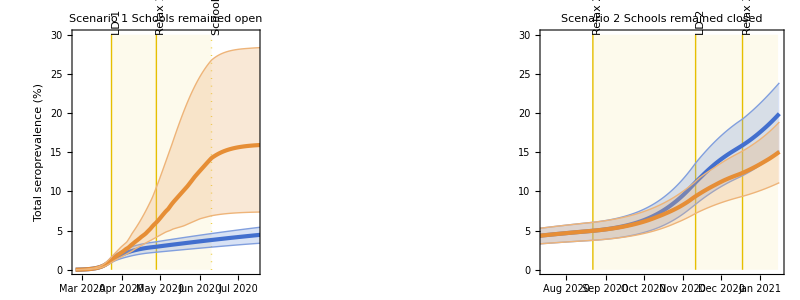
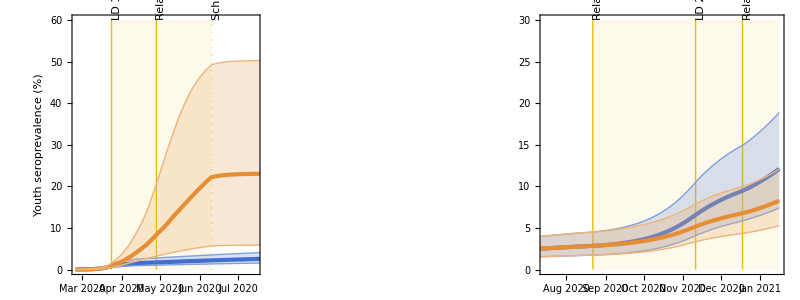
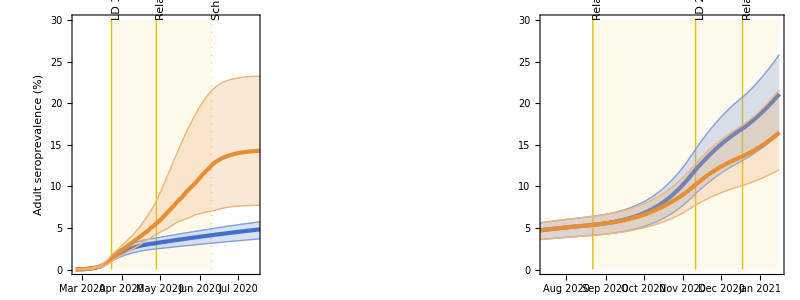

```mathematica
(* Plotting *)
(* We only have one data point on May 28 2020 *)scatterPlotSeroSinglePoint = DateListPlot[{Around[totalMeanSero, {Abs[totalMeanSero - totalLowMeanSero], Abs[totalHighMeanSero-totalMeanSero]}]}, AbsoluteTime["May 28, 2020"], PlotMarkers->{Automatic,10},PlotStyle -> {Black},IntervalMarkers->"Fences",IntervalMarkersStyle->{Black,Thick}, PlotStyle->"Web"];

seroTotal2Plot = {seroprevalenceScenariosTotal[[1,1, All, All]],
seroprevalenceScenariosTotal[[2,1, All, All]],
seroprevalenceScenariosTotal[[3,1, All, All]]};
seroYouth2Plot = {seroprevalenceScenariosGrouped[[1,1, All, All]],
seroprevalenceScenariosGrouped[[2,1, All, All]],
seroprevalenceScenariosGrouped[[3,1, All, All]]};
seroAdult2Plot = {seroprevalenceScenariosGrouped[[1,2, All, All]],
seroprevalenceScenariosGrouped[[2,2, All, All]],
seroprevalenceScenariosGrouped[[3,2, All, All]]};

figSeroTotal= plotScenarioTrajectories[seroTotal2Plot,"Total seroprevalence (%)",{"Scenario 1\nSchools remained open","Scenario 2\nSchools remained closed"},{ticksInvisible,ticksInvisible},{{0,30},{0,30}},{"a", "b"}, "lefter"];
figSeroChild= plotScenarioTrajectories[seroYouth2Plot,"Youth seroprevalence (%)",{"",""},{ticksInvisible,ticksInvisible},{{0,60},{0,30}},{"c", "d"}, "lefter"];
figSeroAdult= plotScenarioTrajectories[seroAdult2Plot,"Adult seroprevalence (%)",{"",""},{ticksVisible,ticksVisible},{{0,30},{0,30}},{"e", "f"}, "lefter"];

figSero = Grid[{{figSeroTotal},{figSeroChild}, {figSeroAdult}}];
exportFigs[figSero, "SFig15"];
```

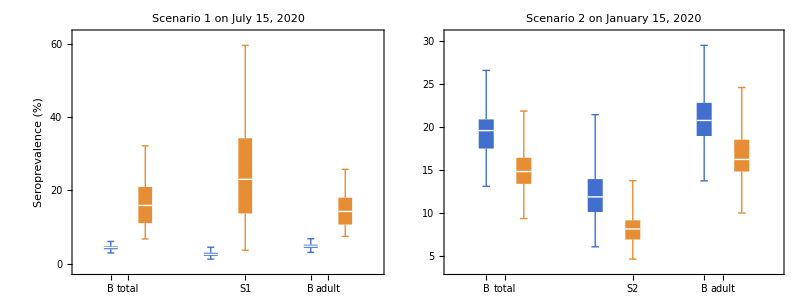

```mathematica
seroEstimates2PlotScen1 = {{seroprevalenceScenariosTotal[[1,1,All,141]],
seroprevalenceScenariosTotal[[2,1,All,141]]},
{seroprevalenceScenariosGrouped[[1,1,All,141]],
seroprevalenceScenariosGrouped[[2,1,All,141]]},
{seroprevalenceScenariosGrouped[[1,2,All,141]],seroprevalenceScenariosGrouped[[2,2,All,141]]}};
seroEstimates2PlotScen2 = {{seroprevalenceScenariosTotal[[1,1,All,325]],
seroprevalenceScenariosTotal[[3,1,All,325]]},
{seroprevalenceScenariosGrouped[[1,1,All,325]],
seroprevalenceScenariosGrouped[[3,1,All,325]]},
{seroprevalenceScenariosGrouped[[1,2,All,325]],seroprevalenceScenariosGrouped[[3,2,All,325]]}};
seroAroundScen1 = Map[getAround, seroEstimates2PlotScen1, {2}];
seroAroundScen2 = Map[getAround, seroEstimates2PlotScen2, {2}];

figSeroScen1BarChart = plotWithLetter[plotBoxWhisker[seroEstimates2PlotScen1, {colorBlue, colorOrange}, {{"total", "youth", "adult"}, {"B", "S1"}}, "", "Seroprevalence (%)", "Scenario 1 on July 15, 2020",1.5],"a", "lefter"];
figSeroScen2BarChart = plotWithLetter[
plotBoxWhisker[seroEstimates2PlotScen2, {colorBlue, colorOrange}, {{"total", "youth", "adult"}, {"B", "S2"}}, "", "", "Scenario 2 on January 15, 2020", 1.5], "b", "lefter"];

figSeroBarChart = Grid[{{figSeroScen1BarChart,figSeroScen2BarChart}}];
exportFigs[figSeroBarChart, "SFig16"];
```

### Uncertainty in the model projections

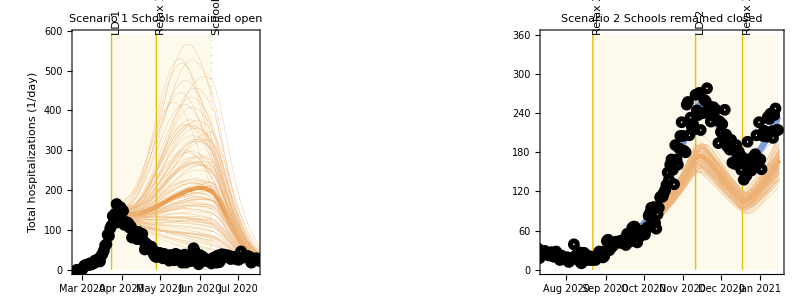
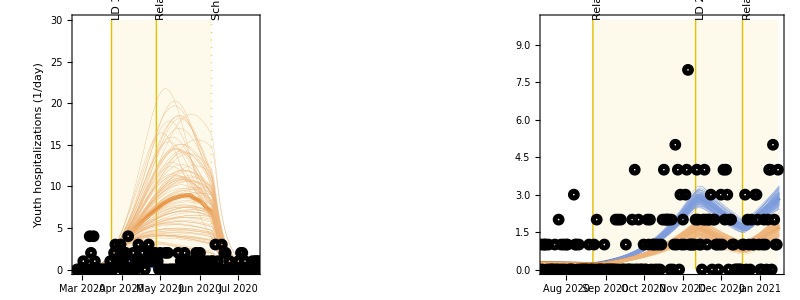

```mathematica
figHospTotalSmooth = plotScenarioTrajectories[hospTot2Plot, "Total hospitalizations (1/day)",{"Scenario 1\nSchools remained open","Scenario 2\nSchools remained closed"},{ticksInvisible, ticksInvisible},{{0,590},{0,360}},{"a", "c"}, "lefter",scatterPlotHospData, 
hospTot2Plot, True];
figHospYouthSmooth = plotScenarioTrajectories[hospYouth2Plot, "Youth hospitalizations (1/day)",{"", ""},{ticksVisible, ticksVisible},{{0,30},{0,10}},{"b", "d"}, "lefter",scatterPlotHospDataChild, 
hospYouth2Plot, True];

figHospTotalYouthSmooth = Grid[{{figHospTotalSmooth}, {figHospYouthSmooth}}];
exportFigs[figHospTotalYouthSmooth, "SFig17"];
```

### Sensitivity analyses for Scenario 1

```mathematica
(* Scenarios done are ran similarly as that of Baseline, Scenario 1, and Scenario 2 but we only attach the generated results in the repo *)
scenarios4Sens = {"Scenario1Point1", "Scenario1Point2", "Scenario2Point1", "Scenario2Point2"};
scenariosShortCodes = {"1relax", "1zeta", "2alt", "2chris"};
scenarioTitles = {"Scenario 1.1","Scenario 1.2", "Scenario 2.1", "Scenario 2.2"};
scenarioBaseIndices = {1,1,2,2};
scenarioMaxRanges =  ConstantArray[0, {Length[scenarios4Sens],Length[measures4Sens],2}];
scenarioMaxRanges[[1]] = {{0, 1300}, {0, 40}, {0, 45}, {0, 65}, {0, 3}, {0, 0.9},  {0, 15},  {0, 4}};
scenarioMaxRanges[[2]] = {{0, 350}, {0, 15}, {0, 20}, {0, 35}, {0, 3}, {0, 0.8},  {0, 15},  {0, 4}};
scenarioMaxRanges[[3]] = {{0, 325}, {0, 10}, {0, 25}, {0, 20}, {0.70, 1.30}, {0.04, 0.25},  {4.5,9},  {0.75,2}};
scenarioMaxRanges[[4]] = {{0, 325}, {0, 10}, {0, 25}, {0, 20}, {0.80, 1.30}, {0.03, 0.25},  {4.5,9},  {0.75, 2.25}};


measures4Sens = {"HOSPITALIZATION","HOSPITALIZATION_SIMULATED","SUSCEPTIBLE","CONTACTS", "EIGEN","ELASTICITY"};
measuresScenarios4Sens = Table[Table[Module[{filePath, state},
filePath=FileNameJoin[{If[meas <5,"../results/solutions/","../results/analysis/"]},StringJoin[measures4Sens[[meas]],"_",scenarios4Sens[[scen]],".wxf"]];
state=Import[filePath,"WXF"];
state
],{scen, 1, Length[scenarios4Sens]}],{meas, 1, Length[measures4Sens]}];

hospitalizationScenarios4Sens = measuresScenarios4Sens[[1,All]];
hospitalizationSimulatedScenarios4Sens = measuresScenarios4Sens[[2,All]];
susceptibleScenarios4Sens = measuresScenarios4Sens[[3,All]];
contactMatricesScenarios4Sens = measuresScenarios4Sens[[4,All]];
RtScenarios4Sens = measuresScenarios4Sens[[5,All]];
elasScenarios4Sens = measuresScenarios4Sens[[6,All]];
```

```mathematica
(* Hospitalizations *)
hospitalizationScenariosGrouped4Sens = summingGroups4Scenarios[hospitalizationScenarios4Sens, groupIndex];
hospitalizationScenariosTotal4Sens = summingGroups4Scenarios[hospitalizationScenarios4Sens, {Range[1, 10]}];
hospitalizationSimulatedScenariosGrouped4Sens = summingGroups4Scenarios[hospitalizationSimulatedScenarios4Sens, groupIndex];
hospitalizationSimulatedScenariosTotal4Sens = summingGroups4Scenarios[hospitalizationSimulatedScenarios4Sens, {Range[1, 10]}];


(* Seroprevalence *)
susceptibleScenariosTotal4Sens = summingGroups4Scenarios[susceptibleScenarios4Sens, {Range[1, 10]}];
susceptibleScenariosGrouped4Sens = summingGroups4Scenarios[susceptibleScenarios4Sens, groupIndex];
seroprevalenceScenariosTotal4Sens = 100-100susceptibleScenariosTotal4Sens/Total[demographyData10];
seroprevalenceScenariosGrouped4Sens = ConstantArray[0, {Length[scenarios4Sens],2,100,327}];
Table[seroprevalenceScenariosGrouped4Sens[[All, k, All, All]]=
100-100susceptibleScenariosGrouped4Sens[[All,k,All,All]]/Total[demographyData10[[groupIndex[[k]]]]];, {k ,1,2}];


(* Average contacts *)
averageContactMatrixTotalScenarios4Sens = contactMatricesScenarios4Sens;
Do[averageContactMatrixTotalScenarios4Sens[[i,j,k,All,All]]=contactMatricesScenarios4Sens[[i,j,k,All,All]]*demographyData1010,{i,1,Length[scenarios4Sens]},{j,1,numSamples},{k,1,numTimes}];
averageContactsTotalScenarios4Sens = Total[averageContactMatrixTotalScenarios4Sens, {5}] / Total[demographyData10];
averageContactsTotal4Sens= Total[averageContactsTotalScenarios4Sens[[All, All, All, Range[1,10]]], {4}];
averageContactsYouth4Sens= Total[averageContactsTotalScenarios4Sens[[All, All, All, Range[1,3]]], {4}];
averageContactsAdults4Sens= Total[averageContactsTotalScenarios4Sens[[All, All, All, Range[4,10]]], {4}];

(* Getting the average contacts for total, and age-specific groups *)
averageContactsTotal= Total[averageContactsTotalScenarios[[All, All, All, Range[1,10]]], {4}];
averageContactsYouth= Total[averageContactsTotalScenarios[[All, All, All, Range[1,3]]], {4}];
averageContactsAdults =Total[averageContactsTotalScenarios[[All, All, All, Range[4,10]]], {4}];


(* Cumulative elasticities *)
cumuElasScenarios4Sens = Table[Table[Table[cumuElasMatrix[elasScenarios4Sens[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}], {i, 1, Length[scenarios4Sens]}];
cumuElasGroupedScenarios4Sens = Table[Table[Total[cumuElasScenarios4Sens[[scen]][[sample]][[time]][[groupIndex[[i]]]]], {i, 1, Length[groupIndex]}], {scen, 1, Length[scenarios4Sens]}, {sample, 1, Length[listSamples]}, {time, 1, numTimes}];
```

```mathematica
(* Plotting *)
baseline4Sens2Plot = {hospitalizationSimulatedScenariosTotal[[1,1, All, All]], hospitalizationSimulatedScenariosGrouped[[1,1, All, All]],
seroprevalenceScenariosTotal[[1,1, All, All]],seroprevalenceScenariosGrouped[[1,1, All, All]],RtScenarios[[1,All,All,1]],cumuElasGroupedScenarios[[1,All,All,1]],averageContactsTotal[[1,All,All]],averageContactsYouth[[1,All,All]]};

measuresScenarios4Sens2Plot[scenarioIndex_] := {hospitalizationSimulatedScenariosTotal4Sens[[scenarioIndex,1, All, All]], hospitalizationSimulatedScenariosGrouped4Sens[[scenarioIndex,1, All, All]],
seroprevalenceScenariosTotal4Sens[[scenarioIndex,1, All, All]],seroprevalenceScenariosGrouped4Sens[[scenarioIndex,1, All, All]],RtScenarios4Sens[[scenarioIndex,All,All,1]],cumuElasGroupedScenarios4Sens[[scenarioIndex,All,All,1]],averageContactsTotal4Sens[[scenarioIndex,All,All]],averageContactsYouth4Sens[[scenarioIndex,All,All]]};

Remove["plotting`*"]
Get["../packages/plotting.m"]

figGrid4Sens[scenarioIndex_] :=Module[{figList},
figList = Table[
plotWithLetter[{plotLineWithCrI[baseline4Sens2Plot[[m]],colorBlue,"","",yLabel4Sens[[m]],scenarioBaseIndices[[scenarioIndex]],If[m <7,ticksInvisible, ticksVisible],scenarioMaxRanges[[scenarioIndex, m]],0.5,500,Solid,Which[m == 1,hospitalizationScenariosTotal[[1,1,All,All]],
m == 2, hospitalizationScenariosGrouped[[1,1,All,All]],
True, {}], False, scenariosShortCodes[[scenarioIndex]]],

plotLineWithCrI[measuresScenarios4Sens2Plot[scenarioIndex][[m]],colorOrange,"","","",scenarioBaseIndices[[scenarioIndex]],If[m <7,ticksInvisible, ticksVisible],scenarioMaxRanges[[scenarioIndex, m]],0.5,500,Solid,Which[m == 1,hospitalizationScenariosTotal4Sens[[scenarioIndex,1,All,All]],
m == 2, hospitalizationScenariosGrouped4Sens[[scenarioIndex,1,All,All]],
True, {}], False, scenariosShortCodes[[scenarioIndex]]],

Which[m == 1,scatterPlotHospData,
m == 2, scatterPlotHospDataChild,
m == 5, Rt1Line,
True, Graphics[]]
},alphabetLetters[[m]],"lefter"],{m, 1, Length[yLabel4Sens]}];
figGrid = Grid[ArrayReshape[figList, {4,2}]];
figGrid = Grid[{{Style[scenarioTitles[[scenarioIndex]],TextAlignment -> Center,Black,sizeFontBig, FontFamily->"Helvetica"]},{figGrid}}]];
```

i::shdw: Symbol i appears in multiple contexts {plotting`,preliminaries`}; definitions in context plotting` may shadow or be shadowed by other definitions.

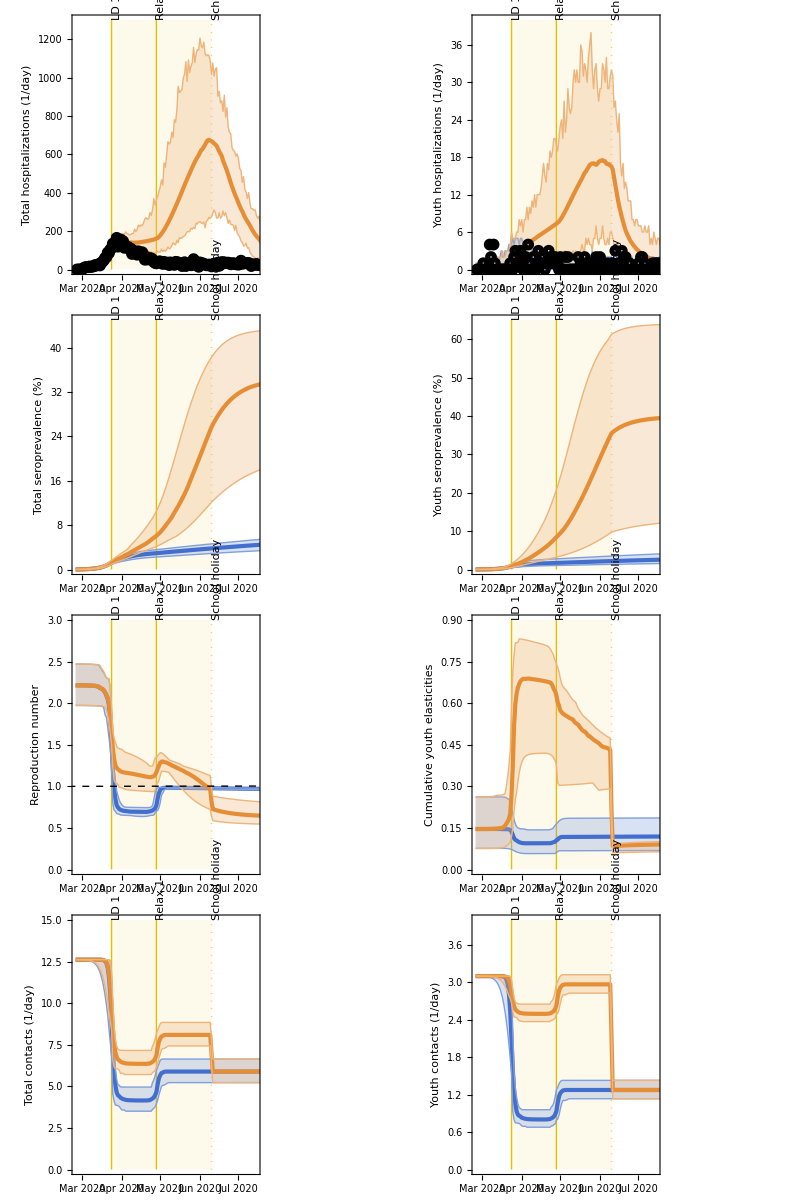
Scenario 1.1
-Graphics-

```mathematica
exportFigs[figGrid4Sens[1],"SFig18"];
```

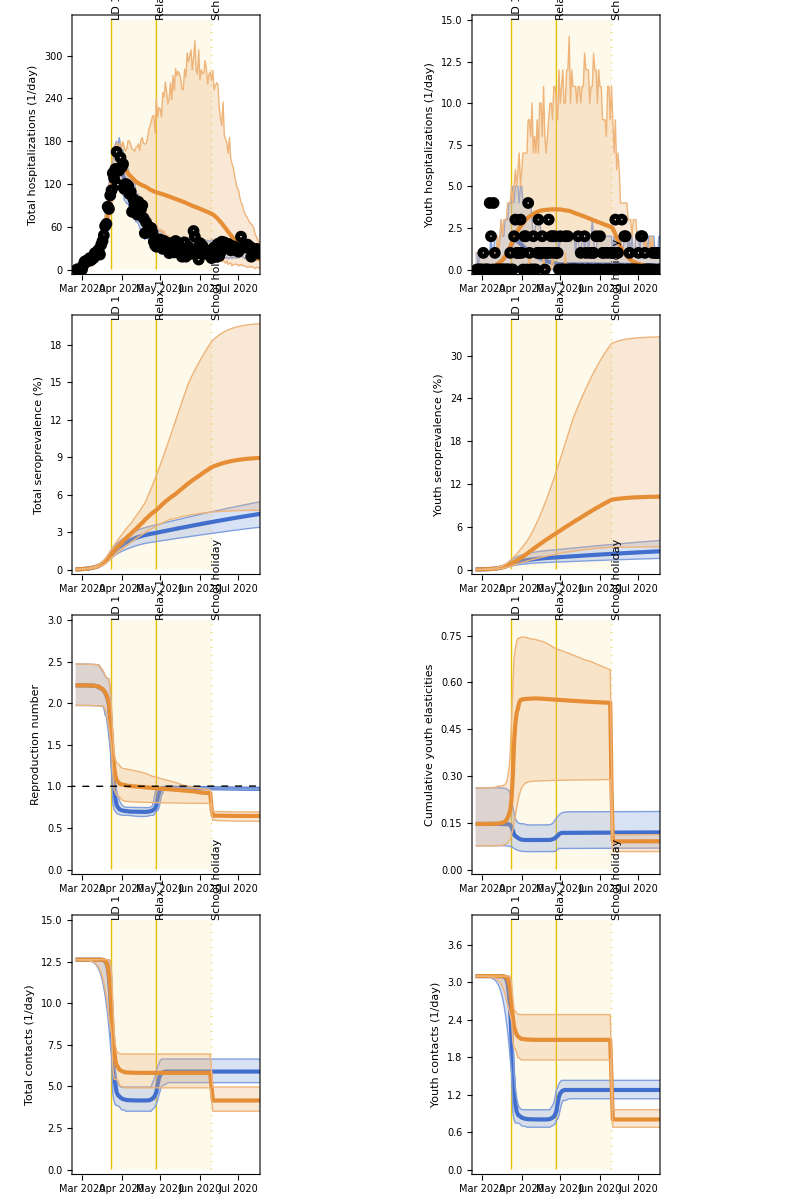
Scenario 1.2
-Graphics-

```mathematica
exportFigs[figGrid4Sens[2],"SFig19"];
```

### Sensitivity analyses for Scenario 2

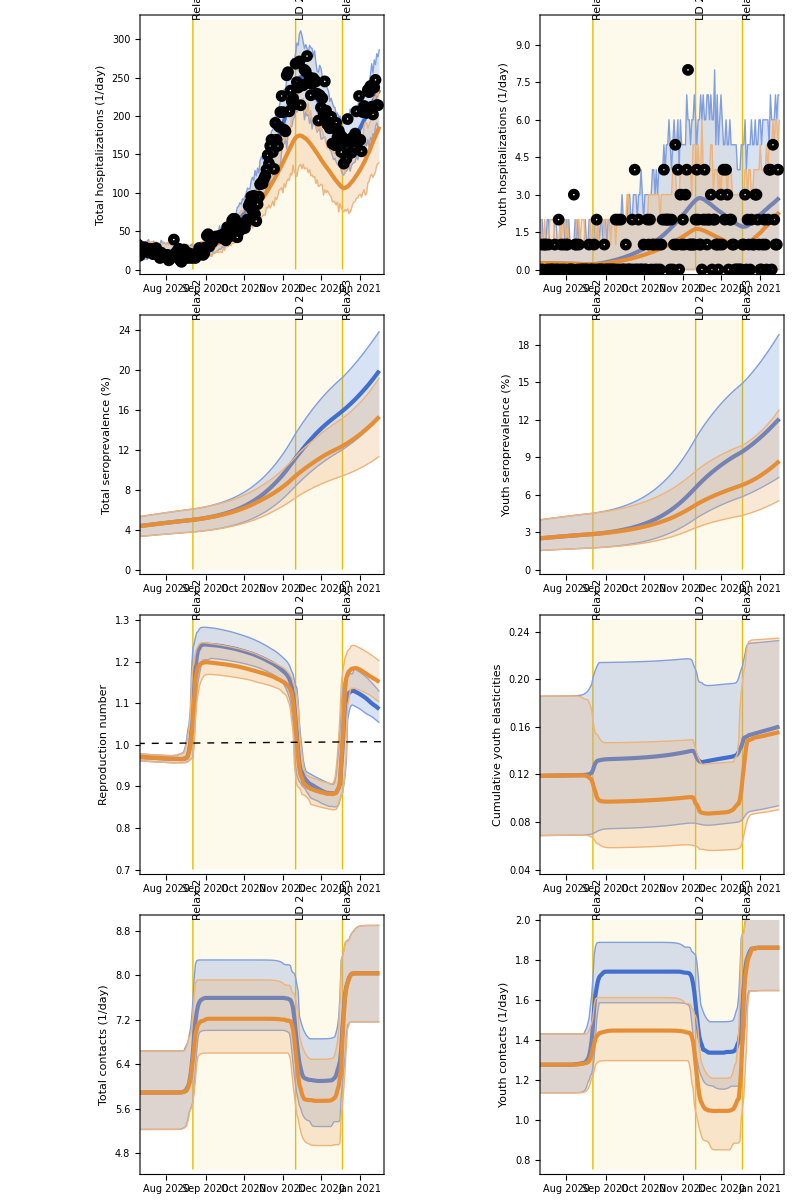
Scenario 2.1
-Graphics-

```mathematica
exportFigs[figGrid4Sens[3],"SFig20"];
```

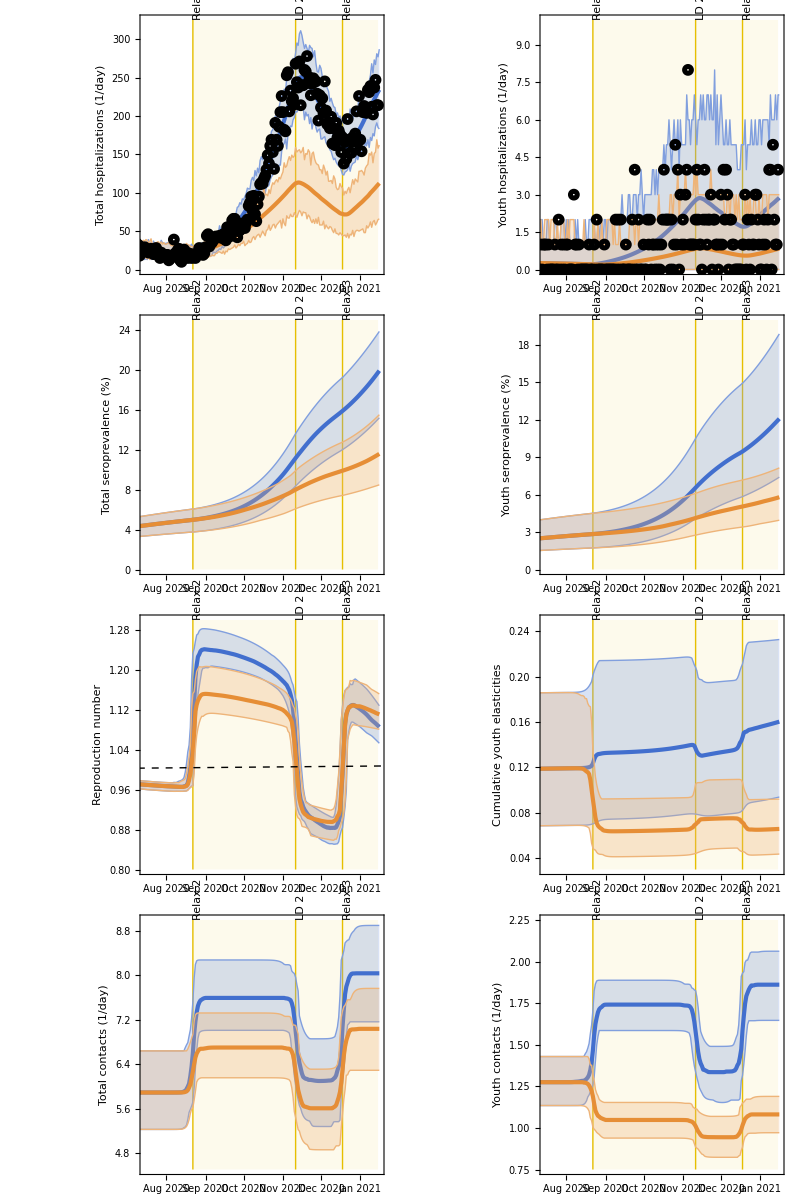
Scenario 2.2
-Graphics-

```mathematica
exportFigs[figGrid4Sens[4],"SFig21"];
```

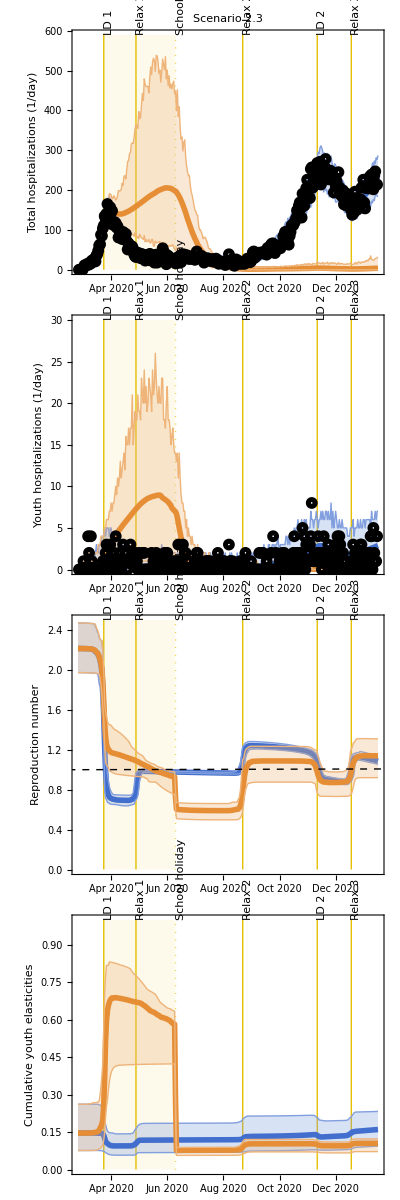

```mathematica
figHospTotal1to2 =
plotWithLetter[{plotLineWithCrI[hospSimulTotal2Plot[[1]],colorBlue,"Scenario 2.3","","Total hospitalizations (1/day)",3,ticksInvisible,{0, 590},0.25,1000,Solid,hospTot2Plot[[1]], False, "1to2"],
plotLineWithCrI[hospSimulTotal2Plot[[2]],colorOrange,"","","",3,ticksInvisible,{0, 590},0.25,1000,Solid,hospTot2Plot[[2]], False, "1to2"],scatterPlotHospData}, "a", "righter"];

figHospYouth1to2 =
plotWithLetter[{plotLineWithCrI[hospSimulYouth2Plot[[1]],colorBlue,"","","Youth hospitalizations (1/day)",3,ticksInvisible,{0, 30},0.25,1000,Solid,hospYouth2Plot[[1]], False, "1to2"],
plotLineWithCrI[hospSimulYouth2Plot[[2]],colorOrange,"","","",3,ticksInvisible,{0, 30},0.25,1000,Solid,hospYouth2Plot[[2]], False, "1to2"],scatterPlotHospDataChild}, "b", "righter"];

figRt1to2 =
plotWithLetter[{plotLineWithCrI[Rt2Plot[[1]],colorBlue,"","","Reproduction number",3,ticksInvisible,{0, 2.5},0.25,1000,Solid, {},False, "1to2"],
plotLineWithCrI[Rt2Plot[[2]],colorOrange,"","","",3, ticksInvisible,{0, 2.5},0.25,1000,Solid,{}, False, "1to2"],Rt1Line}, "c", "righter"];

figCumuElas1to2 =
plotWithLetter[{plotLineWithCrI[cumuElas2Plot[[1]],colorBlue,"","","Cumulative youth elasticities",3,ticksVisible,{0, 1},0.25,1000,Solid, {},False, "1to2"],
plotLineWithCrI[cumuElas2Plot[[2]],colorOrange,"","","",3, ticksVisible,{0, 1},0.25,1000,Solid,{}, False, "1to2"]}, "d", "righter"];


figScenario1to2 = Grid[{{figHospTotal1to2},
{figHospYouth1to2},
{figRt1to2},
{figCumuElas1to2}}];
exportFigs[figScenario1to2, "SFig22"];
```